## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister

```mathematica
SetDirectory["/Users/meister/Temp/Mathematica"]
```

## Setup to generate code that is embeded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

## Bond stretch term between two atoms with coordinates {x1,y1,z1} and {x2,y2,z2} - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

### Define the Hooks law bond stretch potential

```mathematica
stretchDeviation = Sqrt[(bb-ba).(bb-ba)]-r0;
```

```mathematica
stretchEnergyFn =  kb  (stretchDeviation)^2.0
```

```mathematica
names = Flatten[{ba,bb}]
```

### Assemble the energy function rules to expand

```mathematica
stretchVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2}
};
```

```mathematica
stretchSetupRules = {};
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(kb);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(r0);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(I1);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(I2);"]];
```

```mathematica
For[i=1,i≤Length[stretchVarNames],i++,
str = "STRETCH_SET_POSITION("<>ToString[stretchVarNames[[i]][[1]]]<>","<>ToString[stretchVarNames[[i]][[3]]]<>","<>ToString[stretchVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[stretchSetupRules,CCode[str]];
];
```

```mathematica
stretchSetupRules//MatrixForm
```

```mathematica
stretchEnergyRules = {};
stretchOutputs = {};
AppendTo[stretchEnergyRules,Assign[StretchDeviation,stretchDeviation]];
AppendTo[stretchEnergyRules,Assign[Energy,stretchEnergyFn]];
AppendTo[stretchEnergyRules,EnergyAccumulate["STRETCH",Energy]];
AppendTo[stretchOutputs,Energy];
```

### Append the Gradient and Hessian rules

```mathematica
stretchEnergyFn
```

```mathematica
(stretchHessian = Table[Table[0,{6}],{6}])//MatrixForm
```

```mathematica
stretchForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["STRETCH",stretchForceHessianRules,stretchOutputs,stretchHessian,stretchEnergyFn,stretchVarNames];
```

```mathematica
stretchHessian//MatrixForm
```

```mathematica
stretchOutputs
```

### Collect terms and convert to C code

```mathematica
stretchAllRules ={
stretchSetupRules,
stretchEnergyRules,
stretchForceHessianRules};
```

```mathematica
stretchRules = Flatten[stretchAllRules];
```

```mathematica
stretchRules
```

```mathematica
stretchInput = {x1,y1,z1,x2,y2,z2,r0,kb};
```

```mathematica
AppendTo[stretchOutputs,StretchDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
stretchPack0 = {
Name->"Stretch",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
HessianStructure->stretchHessian,
Rules->stretchRules,
Input->stretchInput,
Output->stretchOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[stretchPack0];
```

stretchPack = Block[{PrintTemporary = Print}, packOptimize[stretchPack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
stretchPack = packOptimize[stretchPack0];
```

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

```mathematica
packGraph[stretchPack]
```

## Angle bend term using Mathematica generated gradient/Hessian expansion

```mathematica
Clear[x1,y1,z1,x2,y2,z2,x3,y3,z3,ab,cb,ba,bb,bc];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
bc = { x3, y3, z3 };
```

```mathematica
angleInputs = Flatten[{ba,bb,bc,{t0,kt}}]
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
ab= ba - bb;
cb = bc - bb;
dotNormAbNormCb= Dot[ab,cb]/(vecLen[ab]vecLen[cb]);
fnThetaDev = ArcCos[dotNormAbNormCb]-t0
```

```mathematica
angleEnergyFn =  kt (thetaDev)^2
```

```mathematica
angleEnergyFn = angleEnergyFn/.{thetaDev->fnThetaDev}
```

```mathematica
names = Flatten[{ba,bb,bc}]
```

### Energy

```mathematica
angleVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2},
{x3,x,I3,0},
{y3,y,I3,1},
{z3,z,I3,2}
};
```

```mathematica
angleSetupRules = {};
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(kt);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(t0);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I1);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I2);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I3);"]];
```

```mathematica
For[i=1,i≤Length[angleVarNames],i++,
str = "ANGLE_SET_POSITION("<>ToString[angleVarNames[[i]][[1]]]<>","<>ToString[angleVarNames[[i]][[3]]]<>","<>ToString[angleVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[angleSetupRules,CCode[str]];
];
```

```mathematica
angleSetupRules//MatrixForm
```

```mathematica
angleOutputs = {};
```

```mathematica
angleHessian = Table[Table[0,{9}],{9}]
```

```mathematica
angleEnergyRules = {};
AppendTo[angleEnergyRules,Assign[DotNormAbNormCb,dotNormAbNormCb]];
AppendTo[angleEnergyRules,Assign[AngleDeviation,fnThetaDev]];
AppendTo[angleEnergyRules,CCode["bool IllegalAngle=false;"]];
AppendTo[angleEnergyRules,CCode["if(fabs(DotNormAbNormCb)>(1.0-VERYSMALL)) IllegalAngle=true;"]];
AppendTo[angleEnergyRules,Assign[Energy,angleEnergyFn]];
AppendTo[angleEnergyRules,EnergyAccumulate["ANGLE",Energy]];
AppendTo[angleOutputs,Energy];
```

```mathematica
angleForceHessianRules = {};
AppendGradientForceAndHessian["ANGLE",angleForceHessianRules,angleOutputs,angleHessian,angleEnergyFn,angleVarNames];
```

### Collect and simplify

```mathematica
Length[angleEnergyRules]
```

```mathematica
angleRules = Flatten[{angleSetupRules,angleEnergyRules,angleForceHessianRules}];
```

```mathematica
AppendTo[angleOutputs,AngleDeviation];
```

```mathematica
angleOutputs//FullForm
```

```mathematica
anglePack0 = {
Name->"Angle",
AdditionalCDeclares->"",
EnergyFunction->angleEnergyFn,
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3},
HessianStructure -> angleHessian,
Rules->angleRules,
Input->angleInputs,
Output->angleOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[anglePack0];
```

```mathematica
anglePack = packOptimize[anglePack0];
```

```mathematica
packGraph[anglePack]
```

## Non-bonding terms - Van der Waals and Electrostatic interactions. - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,x2,y2,z2, evdw, eeel,nonbondEquation];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
nonBondInputs = Flatten[{ba,bb,dA,dC,dQ1Q2}]
```

```mathematica
nonbondDistance = Sqrt[Dot[(ba-bb),(ba-bb)]];
```

```mathematica
evdwEquation = (dA/nonbondDistance^12-dC/nonbondDistance^6)
```

```mathematica
eeelEquation = (dQ1Q2/nonbondDistance)
```

```mathematica
nonbondEquation = evdwEquation + eeelEquation
```

```mathematica
names = Flatten[{ba,bb}]
```

### Energy

```mathematica
nonbondVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2}
};
```

```mathematica
nonbondSetupRules = {};
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(I1);"]];
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(I2);"]];AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dA);"]];
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondVarNames],i++,
str = "NONBOND_SET_POSITION("<>ToString[nonbondVarNames[[i]][[1]]]<>","<>ToString[nonbondVarNames[[i]][[3]]]<>","<>ToString[nonbondVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[nonbondSetupRules,CCode[str]];
];
```

```mathematica
nonbondSetupRules//MatrixForm
```

```mathematica
nonbondEnergyRules = {};
nonbondOutputs = {};
AppendTo[nonbondEnergyRules,Assign[NonbondDistance,nonbondDistance]];
AppendTo[nonbondEnergyRules,Assign[Evdw,evdwEquation]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND_EVDW",Evdw]];
AppendTo[nonbondEnergyRules,Assign[Eeel,eeelEquation]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND_EEEL",Eeel]];
AppendTo[nonbondEnergyRules,Assign[Energy,Evdw+Eeel]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND",Energy]];
AppendTo[nonbondOutputs,Energy];
AppendTo[nonbondOutputs,Evdw];
AppendTo[nonbondOutputs,Eeel];
```

```mathematica
nonbondHessian = Table[Table[0,{6}],{6}]
```

```mathematica
nonbondForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["NONBOND",nonbondForceHessianRules,nonbondOutputs,nonbondHessian,nonbondEquation,nonbondVarNames];
```

### Collect and simplify.

```mathematica
AppendTo[nonbondOutputs,NonbondDistance]
```

```mathematica
nonbondOutputs//FullForm
```

```mathematica
nonbondRules = Flatten[{nonbondSetupRules,nonbondEnergyRules,nonbondForceHessianRules}];
```

```mathematica
nbPack0 = {
Name->"Nonbond",
AdditionalCDeclares->"",
EnergyFunction->nonbondEquation,
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
HessianStructure->nonbondHessian,
Rules->nonbondRules,
Input->nonBondInputs,
Output->nonbondOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nbPack0];
```

```mathematica
nbPack = packOptimize[nbPack0];
```

```mathematica
packGraph[nbPack]
```

## Dihedral angle

## Setup the torsion term

```mathematica
Clear[phi,CosNPhi,SinNPhi,Phi];
```

```mathematica
ri = { x1, y1, z1};
rj = { x2, y2, z2};
rk = { x3, y3, z3 };
rl = {x4, y4, z4};
r = Flatten[{ri,rj,rk,rl}];
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
F = ri - rj;
G = rj - rk;
H = rl - rk;
```

```mathematica
A = Cross[F,G];
```

```mathematica
B = Cross[H,G];
```

```mathematica
lenA = vecLen[A];
lenB = vecLen[B];
```

```mathematica
reciprocalLenA = reciprocal[lenA];
reciprocalLenB = reciprocal[lenB];
```

```mathematica
dihedralVarNames = { 
{x1,x,I1,0,DPhiDri},
{y1,y,I1,1,DPhiDri},
{z1,z,I1,2,DPhiDri},
{x2,x,I2,0,DPhiDrj},
{y2,y,I2,1,DPhiDrj},
{z2,z,I2,2,DPhiDrj},
{x3,x,I3,0,DPhiDrk},
{y3,y,I3,1,DPhiDrk},
{z3,z,I3,2,DPhiDrk},
{x4,x,I4,0,DPhiDrl},
{y4,y,I4,1,DPhiDrl},
{z4,z,I4,2,DPhiDrl}
};
```

```mathematica
dihedralSetupRules = {};
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(sinPhase);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(cosPhase);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(V);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(DN);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(IN);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I1);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I2);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I3);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I4);"]];
```

```mathematica
For[i=1,i≤Length[dihedralVarNames],i++,
str = "DIHEDRAL_SET_POSITION("<>ToString[dihedralVarNames[[i]][[1]]]<>","<>ToString[dihedralVarNames[[i]][[3]]]<>","<>ToString[dihedralVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[dihedralSetupRules,CCode[str]];
];
```

```mathematica
dihedralSetupRules//MatrixForm
```

```mathematica
dihedralCosPhiRules = {};
```

```mathematica
AppendTo[dihedralCosPhiRules,lenA->LenA];
AppendTo[dihedralCosPhiRules,lenB->LenB];
AppendTo[dihedralCosPhiRules,reciprocalLenA->ReciprocalLenA];
AppendTo[dihedralCosPhiRules,reciprocalLenB->ReciprocalLenB];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["if (fabs(LenA)<TENM3) ReciprocalLenA = 0.0;"]];
AppendTo[dihedralCosPhiRules,CCode["if (fabs(LenB)<TENM3) ReciprocalLenB = 0.0;"]];
```

```mathematica
recLenArecLenB = ReciprocalLenA*ReciprocalLenB;
```

```mathematica
AppendTo[dihedralCosPhiRules,recLenArecLenB->RecLenARecLenB];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["EraseLinearDihedral = 1.0;"]];
AppendTo[dihedralCosPhiRules,CCode["if (RecLenARecLenB==0.0) EraseLinearDihedral = 0.0;"]];
```

```mathematica
cosPhi = A.B*(RecLenARecLenB);
sinPhi = vecLen[G]*RecLenARecLenB*Dot[A,H];
```

```mathematica
AppendTo[dihedralCosPhiRules,cosPhi->CosPhi];
AppendTo[dihedralCosPhiRules,sinPhi->SinPhi];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["CosPhi=MAX(-1.0,MIN(1.0,CosPhi));"]];
```

phi = ArcCos[CosPhi];

AppendTo[dihedralEnergyRules, phi -> Phi]; (* I don't think I need to evaluate Phi *)

At this point we need to calculate SinNPhi and CosNPhi and we use the function calculateSinNPhiCosNPhi in both C and Mathematica.Insert function sinNPhiCosNPhi[N, &sinNPhi, &cosNPhi, sinPhi, cosPhi] into evaluation

```mathematica
dihedralEnergyRules = dihedralCosPhiRules;
```

```mathematica
AppendTo[dihedralEnergyRules,MathCode["CosNPhi = mathCosNPhi[IN,SinPhi,CosPhi];"]];
AppendTo[dihedralEnergyRules,MathCode["SinNPhi = mathSinNPhi[IN,SinPhi,CosPhi];"]];
```

```mathematica
If[DebugDihedral,
AppendTo[dihedralEnergyRules,MathCode["If[CosPhi>0.1,Phi=ArcSin[SinPhi],
					Phi=ArcCos[CosPhi]*Sign[SinPhi]];"]];
AppendTo[dihedralEnergyRules,CCode["if(CosPhi>0.1){Phi=asin(SinPhi);}else
					{Phi=acos(CosPhi)*SIGN(SinPhi);}"]];
];
```

```mathematica
AppendTo[dihedralEnergyRules,CCode["sinNPhiCosNPhi(IN, &SinNPhi, &CosNPhi, SinPhi, CosPhi);"]];
```

Sum and difference formulas
sin (A + B) = sin A cos B + cos A sin B
sin (A - B) = sin A cos B - cos A sin B
cos (A + B) = cos A cos B - sin A sin B
cos (A - B) = cos A cos B + sin A sin B

```mathematica
cosNPhiPhase =CosNPhi* cosPhase+SinNPhi*sinPhase;
sinNPhiPhase=SinNPhi*cosPhase-CosNPhi*sinPhase;
```

```mathematica
dihedralDeviation = 1.0+cosNPhiPhase; (*between 0.0 and 2.0*)
```

```mathematica
fnETorsion = EraseLinearDihedral * V (dihedralDeviation)
```

fnETorsion = EraseLinearDihedral * V (1.0 + Cos[DN Phi - phase]);

```mathematica
AppendTo[dihedralEnergyRules,Assign[DihedralDeviation,dihedralDeviation]];
AppendTo[dihedralEnergyRules,fnETorsion->Energy];
AppendTo[dihedralEnergyRules,EnergyAccumulate["DIHEDRAL",Energy]];
dihedralOutputs = {};
AppendTo[dihedralOutputs,Energy];
```

```mathematica
dihedralInputs = Flatten[{ri,rj,rk,rl,{V,DN,IN,cosPhase, sinPhase}}]
```

```mathematica
dihedralEnergyFn = fnETorsion/.{Phi->phi}
```

```mathematica
dETorsiondPhi = -EraseLinearDihedral*V*DN*sinNPhiPhase;
```

```mathematica
dihedralGradientRules = {}
```

```mathematica
AppendTo[dihedralGradientRules, Assign[DeDPhi, dETorsiondPhi]];
```

```mathematica
DPhiDri = (-vecLen[G]/(A.A)A);
```

```mathematica
DPhiDrj = (vecLen[G]/(A.A)A+(F.G)/(A.A*vecLen[G])A-(H.G)/(B.B*vecLen[G])B);
```

```mathematica
DPhiDrk =((H.G)/(B.B*vecLen[G])B-(F.G)/(A.A*vecLen[G])A-vecLen[G]/(B.B)B);
```

```mathematica
DPhiDrl = (vecLen[G]/(B.B)B);
```

```mathematica
dPhidr = {};
```

```mathematica
AppendOneDihedralGradientForce[rawMacroPrefix_,be_,dPhidr_,outputs_,rawNameInfo_,rawdEdPhi_]:=Block[
	{fn,gradName,zforceName,nameRules,
	dEdPhi = Evaluate[rawdEdPhi],
	nameInfo=Evaluate[rawNameInfo],
	macroPrefix=Evaluate[rawMacroPrefix],var},
	nameRules = ExtractNames[nameInfo];
	var = Name/.nameRules;
	gradName = Symbol["g"<>ToString[var]];
	zforceName = Symbol["f"<>ToString[var]];
	fn = (Func/.nameRules)[[(Offset/.nameRules)+1]];
	AppendTo[dPhidr,fn];
	AppendTo[be,Assign[gradName,fn*dEdPhi]];
	AppendTo[be,Assign[zforceName,-gradName]];
	AppendTo[be,ForceAccumulate[macroPrefix,nameRules,zforceName]];
	AppendTo[outputs,zforceName];
];
SetAttributes[AppendOneDihedralGradientForce,HoldAll];
```

```mathematica
AppendDihedralGradientForce[rawMacroPrefix_,be_,dPhidr_,outputs_,rawNames_,rawdEdPhi_]:=Block[
	{macroPrefix=Evaluate[rawMacroPrefix],
	dEdPhi = Evaluate[rawdEdPhi],
	names = Evaluate[rawNames]},
	For[i=1,i≤Length[names],i++,
		Print["Appending gradient force for name: ", names[[i]][[1]]];
		AppendOneDihedralGradientForce[macroPrefix,be,dPhidr,outputs,names[[i]],dEdPhi];
	];
];
SetAttributes[AppendDihedralGradientForce,HoldAll];
```

```mathematica
AppendDihedralGradientForce["DIHEDRAL",dihedralGradientRules,dPhidr,dihedralOutputs,dihedralVarNames,DeDPhi];
```

#### Now dPhidr contains the vector derivative of Phi wrt every component in (r)

```mathematica
Length[dPhidr]
```

## Calculate the Second derivatives of d2Edr2

```mathematica
OuterVector[a_,b_] := Outer[Times,a,b];
```

```mathematica
OverlayMatrix[phiMatrix_,xo_,yo_,mat_]:=Block[{x,y,xa,ya},
	For[x=1,x≤3,x++,
		For[y=1,y≤3,y++,
			xa = (xo-1)*3+x;
			ya = (yo-1)*3+y;
			Print["Filling matrix[",xa,",",ya,"] := mat[",x,",",y,"];"];
			phiMatrix[[xa,ya]]= mat[[x]][[y]];
			If[xa≠ya,phiMatrix[[ya,xa]]= mat[[x]][[y]]];
		];
	];
];
SetAttributes[OverlayMatrix,HoldFirst];
```

```mathematica
OverlaySymmetricMatrix[phiMatrix_,xo_,yo_,mat_]:=Block[{},
	OverlayMatrix[phiMatrix,xo,yo,mat];
];
SetAttributes[OverlaySymmetricMatrix,HoldFirst];
```

```mathematica
(*According to the paper, this is what the Outer product of two matrices should be *)
MatrixOuter[a_,b_] := Block[{m},
m = Table[Table[0,{Length[a]}],{Length[b]}];
For[i=1,i≤Length[a],i++,
For[j=1,j≤Length[a],j++,
m[[i,j]]=a[[i]].b[[j]];
];
];
m
];
```

```mathematica
dPhi2dFGHdFGH = Table[Table[0,{9}],{9}];
```

```mathematica
dPhi2dFGHdFGH//MatrixForm
```

```mathematica
(*Equation 32*)
dPhi2dFdF=vecLen[G]/((A.A)(A.A))(OuterVector[A,Cross[G,A]]+OuterVector[Cross[G,A],A]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,1,dPhi2dFdF];
```

```mathematica
If[DebugDihedral,1]
```

```mathematica
(*Equation 33*)
dPhi2dHdH=(-vecLen[G])/((B.B)(B.B))(OuterVector[B,Cross[G,B]]+OuterVector[Cross[G,B],B]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,3,3,dPhi2dHdH];
```

```mathematica
(*Equation 38, this one has the weird subscripts but I'm just going to assume its simple*)
dPhi2dFdG = 1/(vecLen[G](A.A)(A.A))((G.G)OuterVector[Cross[A,F](*F*),A(*G*)]+(F.G)OuterVector[A(*F*),Cross[A,G](*G*)]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,2,dPhi2dFdG];
```

#### Equation (39), this one needs to be transposed wrt the equation described in the paper.

```mathematica
dPhi2dGdH =Transpose[-1/(vecLen[G](B.B)(B.B))((G.G)OuterVector[Cross[B,H](*H*),B(*G*)]+(H.G)OuterVector[B(*H*),Cross[B,G](*G*)])];OverlaySymmetricMatrix[dPhi2dFGHdFGH,2,3,dPhi2dGdH];
```

```mathematica
(*Equation 40*)
dPhi2dFdH = Table[Table[0,{3}],{3}];
```

```mathematica
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,3,dPhi2dFdH]
```

```mathematica
(*Equation 44*)
dPhi2dGdG=(1/(2(vecLen[G]^3)(A.A))(OuterVector[Cross[G,A],A]+OuterVector[A,Cross[G,A]]))+((F.G)/(vecLen[G](A.A)(A.A))(OuterVector[A,Cross[F,A]]+OuterVector[Cross[F,A],A]))+(-1/(2(vecLen[G]^3)(B.B))(OuterVector[Cross[G,B],B]+OuterVector[B,Cross[G,B]]))+((-(H.G))/(vecLen[G](B.B)(B.B))(OuterVector[B,Cross[H,B]]+OuterVector[Cross[H,B],B]));
```

```mathematica
OverlaySymmetricMatrix[dPhi2dFGHdFGH,2,2,dPhi2dGdG];
```

```mathematica
Dimensions[dPhi2dFGHdFGH]
```

#### At this point (dPhi2dFGHdFGH) should represent the first term in equation 29

```mathematica
(dFGHdr=D[Flatten[{F,G,H}],{Flatten[{ri,rj,rk,rl}]}])//MatrixForm
```

#### Let' s try a scalar product between dPhi2dFGHdFGH and dFGHdr

```mathematica
dihedralProd1 = dPhi2dFGHdFGH.dFGHdr;
```

```mathematica
Dimensions[dihedralProd1]
```

#### Now try a matrix outer product between (prod1) and dFGHdr.

```mathematica
d2Phidr2 = MatrixOuter[Transpose[dihedralProd1],Transpose[dFGHdr]];
```

```mathematica
Dimensions[d2Phidr2]
```

#### d2Phidr2 Should contain the product of equation 29

```mathematica
Transpose[dFGHdr]//MatrixForm
```

```mathematica
(*dETorsiondPhi = -EraseLinearDihedral*dihedralScale*V*DN*sinNPhiPhase;*)
```

## Assemble equation 28, the final equation for the second derivative, it should be a 12x12 matrix

```mathematica
d2EdPhi2 = -V*DN*DN*cosNPhiPhase;
```

```mathematica
d2Edr2 = OuterVector[(d2EdPhi2*dPhidr),dPhidr]+DeDPhi*d2Phidr2;
```

```mathematica
Dimensions[d2Edr2]
```

#### Assemble the names of the second derivatives

dihedralVarNames = { 
   {x1, x, I1, 0, DPhiDri},
   {y1, y, I1, 1, DPhiDri},
   {z1, z, I1, 2, DPhiDri},
   {x2, x, I2, 0, DPhiDrj},
   {y2, y, I2, 1, DPhiDrj},
   {z2, z, I2, 2, DPhiDrj},
   {x3, x, I3, 0, DPhiDrk},
   {y3, y, I3, 1, DPhiDrk},
   {z3, z, I3, 2, DPhiDrk},
   {x4, x, I4, 0, DPhiDrl},
   {y4, y, I4, 1, DPhiDrl},
   {z4, z, I4, 2, DPhiDrl}
   };

#### Setup the Diagonal Hessian rules

```mathematica
AppendDihedralOneHessianElement[macroPrefix_, be_, outputs_,hessianStructure_, rawHessianFn_, names_, i_, j_] := Module[
   	{name1Info, name2Info, var1Name, var2Name,hessianName,prefix, hess},
   	name1Info = ExtractNames[names[[i]]];
   	name2Info = ExtractNames[names[[j]]];
   	var1Name = Name /. name1Info;
   	var2Name = Name /. name2Info;
		If[i==j,prefix="d",prefix="o"];
   	hessianName = Symbol[prefix<>"h" <> ToString[var1Name] <> ToString[var2Name]];
   	hess = Evaluate[rawHessianFn][[i,j]];
   	AppendTo[be, Assign[hessianName, hess]];
   	AppendTo[outputs, hessianName];
   	AppendTo[be, HessianAccumulate[macroPrefix, name1Info, name2Info, hessianName]];
   	Print["Appended hessian element (", j, ",", i, ") for variable: ", ToString[hessianName]];
		hessianStructure[[i,j]]=Length[outputs];
		If [i≠j,hessianStructure[[j,i]]=Length[outputs]];
   ];
SetAttributes[AppendDihedralOneHessianElement, HoldAll];
```

```mathematica
AppendDihedralDiagonalHessian[macroPrefix_,be_,outputs_,hessianStructure_,rawHessianFn_,names_]:= Module[ {i},
	For[i=1,i≤Length[d2Edr2],i++,
		AppendDihedralOneHessianElement[macroPrefix<>"_DIAGONAL",be,outputs,hessianStructure,rawHessianFn,names,i,i];
	];
];
SetAttributes[AppendDihedralDiagonalHessian, HoldAll];
```

```mathematica
Length[d2Edr2]
```

For[i = 1, i <= Length[d2Edr2], i++,
  AppendDihedralOneHessianElement["DIHEDRAL", dihedralDiagonalHessianRules, dihedralOutputs, d2Edr2, dihedralVarNames, i, i];
  ];

```mathematica
dihedralHessian = Table[Table[0,{12}],{12}]
```

```mathematica
dihedralDiagonalHessianRules = {};AppendDihedralDiagonalHessian["DIHEDRAL",dihedralDiagonalHessianRules,dihedralOutputs,dihedralHessian,d2Edr2,dihedralVarNames];
```

#### Setup the Off Diagonal Hessian rules

```mathematica
AppendDihedralOffDiagonalHessian[macroPrefix_,be_,outputs_,hessianStructure_,rawHessianFn_,names_]:= Module[ {i,j},
	For[i=1,i≤Length[d2Edr2]-1,i++,
		For[j=i+1,j≤Length[d2Edr2],j++,
			AppendDihedralOneHessianElement[macroPrefix<>"_OFF_DIAGONAL",be,outputs,hessianStructure,rawHessianFn,names,i,j];
		];
	];
];
SetAttributes[AppendDihedralOffDiagonalHessian, HoldAll];
```

```mathematica
dihedralOffDiagonalHessianRules = {};AppendDihedralOffDiagonalHessian["DIHEDRAL",dihedralOffDiagonalHessianRules,dihedralOutputs,dihedralHessian,d2Edr2,dihedralVarNames];
```

For[i = 1, i <= Length[d2Edr2] - 1, i++,
  For[j = i + 1, j <= Length[d2Edr2], j++,
    AppendDihedralOneHessianElement["DIHEDRAL", dihedralOffDiagonalHessianRules, dihedralOutputs, d2Edr2, dihedralVarNames, i, j];
    ];
  ];

```mathematica
dihedralAllRules = {};
AppendTo[dihedralAllRules,dihedralSetupRules];
AppendTo[dihedralAllRules,dihedralEnergyRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_FORCE //["]];
AppendTo[dihedralAllRules,CCode["if (calcForce ) {" ]];
AppendTo[dihedralAllRules,dihedralGradientRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_DIAGONAL_HESSIAN //["]];
AppendTo[dihedralAllRules,CCode["if (calcDiagonalHessian) {" ]];
AppendTo[dihedralAllRules,dihedralDiagonalHessianRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_OFF_DIAGONAL_HESSIAN //["]];
AppendTo[dihedralAllRules,CCode["if (calcOffDiagonalHessian) { "]];
AppendTo[dihedralAllRules,dihedralOffDiagonalHessianRules];
AppendTo[dihedralAllRules,CCode["} /*calcOffDiagonalHessian*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_OFF_DIAGONAL_HESSIAN ]"]];
AppendTo[dihedralAllRules,CCode["} /*calcDiagonalHessian*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_DIAGONAL_HESSIAN ]"]];
AppendTo[dihedralAllRules,CCode["} /*calcForce*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_FORCE ]"]];
```

```mathematica
AppendTo[dihedralOutputs,DihedralDeviation];
```

```mathematica
dihedralFlattenedRules = Flatten[dihedralAllRules];
```

```mathematica
If[DebugDihedral,
AppendTo[dihedralOutputs,Phi];
];
```

```mathematica
dihedralPack0 = {
Name->"Dihedral",
AdditionalCDeclares->"",
EnergyFunction->"NotUsed",
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4},
HessianStructure->dihedralHessian,
Rules->dihedralFlattenedRules,
Input->dihedralInputs,
Output->dihedralOutputs
};
```

```mathematica
PlusOptimize = False;
TimesOptimize = False;
```

```mathematica
writeOutputVariablesForDebugging[dihedralPack0];
```

```mathematica
dihedralPack=packOptimize[dihedralPack0];
```

```mathematica
packGraph[dihedralPack]
```

## An improved improper restraint with no discontinuities

```mathematica
improperRestraintSetupRules = {};
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(K);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(U);"]];AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(L);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I1);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I2);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I3);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I4);"]];
```

```mathematica
For[i=1,i≤Length[dihedralVarNames],i++,
str = "IMPROPER_RESTRAINT_SET_POSITION("<>ToString[dihedralVarNames[[i]][[1]]]<>","<>ToString[dihedralVarNames[[i]][[3]]]<>","<>ToString[dihedralVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[improperRestraintSetupRules,CCode[str]];
];
```

```mathematica
improperRestraintSetupRules//MatrixForm
```

```mathematica
Clear[Phi,CosNPhi,SinNPhi];
```

### Here is what it looks like

```mathematica
rad[h_] := h*0.0174533
```

```mathematica
Plot[1-Cos[phi//rad],{phi,0,180}]
```

```mathematica
rawRestraintFn[phi_,L_,U_] := (1-Cos[((phi-L)/(U-L)360)//rad])^3
```

```mathematica
otherRestraintFn[phi_,L_,U_] := (1-Cos[((If[phi>=L,phi,phi+360]-L)/(U+360-L)360)//rad])^3
```

```mathematica
LGreaterThanU[phi_,L_,U_] :=Block[{},
If[(phi<L)&&(phi>U),
0.0,
otherRestraintFn[phi,L,U]
]
]
```

```mathematica
LLessThanU[phi_,L_,U_]:=If[(phi<L)||(phi>U),0.0,rawRestraintFn[phi,L,U]]
```

```mathematica
restraint[phi_,L_,U_]:=If[L<U,LLessThanU[phi,L,U],LGreaterThanU[phi,L,U]]
```

```mathematica
Plot[restraint[phi,-130,130],{phi,-180,180}]
```

```mathematica
Plot[restraint[phi,140,100],{phi,-180,180},PlotRange->All]
```

```mathematica
Plot[restraint[phi,140,140],{phi,-180,180},PlotRange->All]
```

Setup the improper torsion term
We reuse the code for the dihedral term,
specifically we start with:   dihedralCosPhiRules

```mathematica
Clear[Phi]
```

Sum and difference formulas
sin (A + B) = sin A cos B + cos A sin B
sin (A - B) = sin A cos B - cos A sin B
cos (A + B) = cos A cos B - sin A sin B
cos (A - B) = cos A cos B + sin A sin B

```mathematica
improperRestraintOutputs = {};
```

```mathematica
improperRestraintTestRules = dihedralCosPhiRules;
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["If[CosPhi>0.1,Phi=ArcSin[SinPhi],
					Phi=ArcCos[CosPhi]*Sign[SinPhi]];"]];
AppendTo[improperRestraintTestRules,CCode["if(CosPhi>0.1){Phi=asin(SinPhi);}else
					{Phi=acos(CosPhi)*SIGN(SinPhi);}"]];
```

#### At this point we have calculated Phi

```mathematica
AppendTo[improperRestraintTestRules,MathCode["RestraintActive = False;"]];
AppendTo[improperRestraintTestRules,CCode["RestraintActive=false;"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["UShift = 0.0; PhiShift=0.0;"]];
AppendTo[improperRestraintTestRules,CCode["UShift = 0.0; PhiShift = 0.0;"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["
If[ L<U && ((L<=Phi)&&(Phi<=U)), 
	RestraintActive = True;
	UShift = 0.0;
	PhiShift = 0.0;
];
"]];
AppendTo[improperRestraintTestRules,CCode[       "
if( L<U && (L<Phi)&&(Phi<U) ) {
	RestraintActive = true;
	UShift = 0.0;
	PhiShift = 0.0;
}"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["
If[ U<=L && ((Phi<=U)||(Phi>=L)),
	RestraintActive = True;
	UShift = TWOPI;
	If[Phi>=L,
		PhiShift = 0.0;
	,
		PhiShift = TWOPI;
	];
];"]];
AppendTo[improperRestraintTestRules,CCode["
if ( U<=L && ((Phi<=U)||(Phi>=L))) {
	RestraintActive = true;
	UShift = TWOPI;
	if ( Phi>=L ) {
		PhiShift = 0.0;
	} else {
		PhiShift = TWOPI;
	}
}"]];
```

```mathematica
MacroCall[name_,value_] := CCode[name<>"("<>ToString[value]<>");"];
```

### At this point we have the improperRestraintTestRules defined

AppendTo[improperRestraintEnergyRules, MathCode["If[RestraintActive,"]];
AppendTo[improperRestraintEnergyRules, CCode["if(RestraintActive){"]];

```mathematica
improperRestraintEnergyRules = {};
```

```mathematica
psi = (Phi+PhiShift-L)/(U+UShift-L)TWOPI
```

```mathematica
AppendTo[improperRestraintEnergyRules,Assign[Psi,psi]];
```

```mathematica
fnEImproperRestraint = EraseLinearDihedral*K (1-Cos[Psi])^3
```

```mathematica
AppendTo[improperRestraintEnergyRules,Assign[Energy,fnEImproperRestraint]];
```

```mathematica
AppendTo[improperRestraintOutputs,Energy];
AppendTo[improperRestraintEnergyRules,EnergyAccumulate["IMPROPER_RESTRAINT",Energy]];
```

#### Here we have the improperRestraintEnergyRules defined

```mathematica
improperRestraintInputs = Flatten[{ri,rj,rk,rl,{K,L,U}}]
```

```mathematica
fnEImproperRestraintWrtPhi = fnEImproperRestraint/.{Psi->psi}
```

```mathematica
dEImproperRestraintDPhi= D[fnEImproperRestraintWrtPhi,Phi]
```

```mathematica
d2EImproperRestraintDPhi2 = D[dEImproperRestraintDPhi,Phi]
```

```mathematica
improperRestraintVarNames= dihedralVarNames;
```

```mathematica
improperRestraintGradientRules = {};
AppendTo[improperRestraintGradientRules,Assign[DEImproperRestraintDPhi,dEImproperRestraintDPhi]];
improperDPhiDr = {};
AppendDihedralGradientForce["IMPROPER_RESTRAINT",improperRestraintGradientRules,improperDPhiDr, improperRestraintOutputs, improperRestraintVarNames, DEImproperRestraintDPhi ];
```

```mathematica
improperRestraintD2Edr2 = OuterVector[(d2EImproperRestraintDPhi2*dPhidr),dPhidr]+dEImproperRestraintDPhi*d2Phidr2;
```

```mathematica
Dimensions[improperRestraintD2Edr2]
```

```mathematica
improperRestraintHessian = Table[Table[0,{12}],{12}]
```

```mathematica
improperRestraintDiagonalHessianRules = {};AppendDihedralDiagonalHessian["IMPROPER_RESTRAINT",improperRestraintDiagonalHessianRules,improperRestraintOutputs,improperRestraintHessian, improperRestraintD2Edr2,improperRestraintVarNames];
```

```mathematica
improperRestraintOffDiagonalHessianRules = {};AppendDihedralOffDiagonalHessian["IMPROPER_RESTRAINT",improperRestraintOffDiagonalHessianRules,improperRestraintOutputs,improperRestraintHessian,improperRestraintD2Edr2,improperRestraintVarNames];
```

```mathematica
InitializeOutputs[outputs_] := Block[{zeroOutputs},
	zeroOutputs = Map[ToString[#]<>"= 0.0;\n"&,outputs];
	Return[StringJoin[zeroOutputs]];
];
```

```mathematica
improperRestraintAllRules = {};
AppendTo[improperRestraintAllRules,improperRestraintSetupRules];
(* take out setting variables to zero *)
(* AppendTo[improperRestraintAllRules,CCode[InitializeOutputs[improperRestraintOutputs]]]; *)
AppendTo[improperRestraintAllRules,MathCode[InitializeOutputs[improperRestraintOutputs]]];
AppendTo[improperRestraintAllRules,improperRestraintTestRules];
AppendTo[improperRestraintAllRules,MathCode["If[RestraintActive," ]];
AppendTo[improperRestraintAllRules,CCode["if (RestraintActive ) {" ]];AppendTo[improperRestraintAllRules,improperRestraintEnergyRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_FORCE //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcForce ) {" ]];
AppendTo[improperRestraintAllRules,improperRestraintGradientRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_DIAGONAL_HESSIAN //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcDiagonalHessian) {" ]];
AppendTo[improperRestraintAllRules,improperRestraintDiagonalHessianRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcOffDiagonalHessian) { "]];
AppendTo[improperRestraintAllRules,improperRestraintOffDiagonalHessianRules];
AppendTo[improperRestraintAllRules,CCode["} /*calcOffDiagonalHessian*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*calcDiagonalHessian*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_DIAGONAL_HESSIAN ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*calcForce*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_FORCE ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*RestraintActive*/"]];
AppendTo[improperRestraintAllRules,MacroCall["IMPROPER_RESTRAINT_PHI_SET",Phi]];
AppendTo[improperRestraintOutputs,Phi];
AppendTo[improperRestraintAllRules, MathCode["]; (*RestraintActive*)"]];
```

```mathematica
improperRestraintFlattenedRules = Flatten[improperRestraintAllRules];
```

```mathematica
improperRestraintOutputs
```

```mathematica
improperRestraintPack0 = {
Name->"ImproperRestraint",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4},
HessianStructure->improperRestraintHessian,
Rules->improperRestraintFlattenedRules,
Input->improperRestraintInputs,
Output->improperRestraintOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[improperRestraintPack0];
```

```mathematica
improperRestraintPack=packOptimize[improperRestraintPack0];
```

```mathematica
packGraph[improperRestraintPack]
```

## Chiral Restraint - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
va = { x1, y1, z1};
vb = { x2, y2, z2 };
vc = { x3, y3, z3 };
vd = { x4, y4, z4 };
```

```mathematica
Clear[ac,bc,dc];
ac = va-vc;
bc = vb - vc;
dc = vd - vc;
```

```mathematica
Clear[K];
```

```mathematica
chiralRestraintTestFn =  K ((Cross[ac,bc].dc)/(vecLen[ac]vecLen[bc]vecLen[dc])+CO)^3
```

```mathematica
chiralRestraintEnergyFn = chiralRestraintTestFn;
```

```mathematica
names = Flatten[{va,vb,vc,vd}]
```

### Energy function

```mathematica
chiralRestraintVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2},
{x3,x,I3,0},
{y3,y,I3,1},
{z3,z,I3,2},
{x4,x,I4,0},
{y4,y,I4,1},
{z4,z,I4,2}
};
```

```mathematica
chiralRestraintSetupRules = {};
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(K);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(CO);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I1);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I2);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I3);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I4);"]];
```

```mathematica
Block[{i,str},
For[i=1,i≤Length[chiralRestraintVarNames],i++,
str = "CHIRAL_RESTRAINT_SET_POSITION("<>ToString[chiralRestraintVarNames[[i]][[1]]]<>","<>ToString[chiralRestraintVarNames[[i]][[3]]]<>","<>ToString[chiralRestraintVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[chiralRestraintSetupRules,CCode[str]];
];
];
```

```mathematica
chiralRestraintSetupRules//MatrixForm
```

```mathematica
chiralRestraintOutputs = {};
chiralRestraintTestRules = {};
AppendTo[chiralRestraintTestRules,Assign[ChiralTest,chiralRestraintTestFn]]; 
(* We will test the Energy, if its greater than zero then the restraint is active *)
chiralRestraintEnergyRules = {};
AppendTo[chiralRestraintEnergyRules,CCode["Energy=ChiralTest;"]];
AppendTo[chiralRestraintEnergyRules,MathCode["Energy = ChiralTest;"]];
AppendTo[chiralRestraintEnergyRules,EnergyAccumulate["CHIRAL_RESTRAINT",Energy]];
AppendTo[chiralRestraintOutputs,Energy];
```

```mathematica
chiralRestraintTestRules
```

```mathematica
chiralRestraintEnergyRules
```

### Gradient and Hessian

```mathematica
chiralRestraintEnergyFn
```

```mathematica
(chiralRestraintHessian = Table[Table[0,{12}],{12}])//MatrixForm
```

```mathematica
chiralRestraintForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["CHIRAL_RESTRAINT",chiralRestraintForceHessianRules,chiralRestraintOutputs,chiralRestraintHessian,chiralRestraintEnergyFn,chiralRestraintVarNames];
```

```mathematica
chiralRestraintHessian//MatrixForm
```

```mathematica
chiralRestraintOutputs
```

### Collect terms and convert to C code

```mathematica
chiralRestraintAllRules ={};
AppendTo[chiralRestraintAllRules,chiralRestraintSetupRules];
(* take out setting variables to zero *)
(* AppendTo[chiralRestraintAllRules,CCode[InitializeOutputs[chiralRestraintOutputs]]]; *)
AppendTo[chiralRestraintAllRules,chiralRestraintTestRules];
AppendTo[chiralRestraintAllRules,MathCode["If[ChiralTest>0.0," ]];
AppendTo[chiralRestraintAllRules,CCode["if (ChiralTest>0.0 ) {" ]];
AppendTo[chiralRestraintAllRules,chiralRestraintEnergyRules];
AppendTo[chiralRestraintAllRules,chiralRestraintForceHessianRules];
AppendTo[chiralRestraintAllRules,CCode["} /*ChiralTest>0.0*/"]];
```

```mathematica
chiralRestraintRules = Flatten[chiralRestraintAllRules];
```

```mathematica
chiralRestraintInput = Flatten[{va,vb,vc,vd,K,CO}];
```

```mathematica
chiralRestraintPack0 = {
Name->"ChiralRestraint",
AdditionalCDeclares->"",
DerivativeVariables->Flatten[{va,vb,vc,vd}],
HessianStructure->chiralRestraintHessian,
Rules->chiralRestraintRules,
Input->chiralRestraintInput,
Output->chiralRestraintOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[chiralRestraintPack0];
```

```mathematica
chiralRestraintPack = packOptimize[chiralRestraintPack0];
```

```mathematica
packGraph[chiralRestraintPack]
```

## Cartesian anchor term. Anchor atoms at a specific position with a harmonic potential - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2,ka];
```

```mathematica
bx = { x1, y1, z1};
ba = { xa, ya, za };
```

```mathematica
anchorDeviation = (bx-ba).(bx-ba);
```

```mathematica
anchorEnergyFn =  ka  (anchorDeviation)
```

```mathematica
names = Flatten[{bx}]
```

### Energy function

```mathematica
anchorVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
anchorSetupRules = {};
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(ka);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(xa);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(ya);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(za);"]];AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(I1);"]];
```

```mathematica
For[i=1,i≤Length[anchorVarNames],i++,
str = "ANCHOR_RESTRAINT_SET_POSITION("<>ToString[anchorVarNames[[i]][[1]]]<>","<>ToString[anchorVarNames[[i]][[3]]]<>","<>ToString[anchorVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[anchorSetupRules,CCode[str]];
];
```

```mathematica
anchorSetupRules//MatrixForm
```

```mathematica
anchorEnergyRules = {};
anchorOutputs = {};
AppendTo[anchorEnergyRules,Assign[AnchorDeviation,anchorDeviation]];
AppendTo[anchorEnergyRules,Assign[Energy,anchorEnergyFn]];
AppendTo[anchorEnergyRules,EnergyAccumulate["ANCHOR_RESTRAINT",Energy]];
AppendTo[anchorOutputs,Energy];
```

### Gradient and Hessian

```mathematica
anchorEnergyFn
```

```mathematica
(anchorHessian = Table[Table[0,{6}],{6}])//MatrixForm
```

```mathematica
anchorForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["ANCHOR_RESTRAINT",anchorForceHessianRules,anchorOutputs,anchorHessian,anchorEnergyFn,anchorVarNames];
```

```mathematica
anchorHessian//MatrixForm
```

```mathematica
anchorOutputs
```

### Collect terms and convert to C code

```mathematica
anchorAllRules ={
anchorSetupRules,
anchorEnergyRules,
anchorForceHessianRules};
```

```mathematica
anchorRules = Flatten[anchorAllRules];
```

```mathematica
anchorRules//MatrixForm
```

```mathematica
anchorInput = {x1,y1,z1,xa,ya,za,ka};
```

```mathematica
AppendTo[anchorOutputs,AnchorDeviation];
```

```mathematica
anchorPack0 = {
Name->"AnchorRestraint",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1},
HessianStructure->anchorHessian,
Rules->anchorRules,
Input->anchorInput,
Output->anchorOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[anchorPack0];
```

anchorPack = Block[{PrintTemporary = Print}, packOptimize[anchorPack0]];

```mathematica
anchorPack = packOptimize[anchorPack0];
```

Ignore errors in packGraph[anchorPack], I forget what it doesn't like but it is something non-essential

```mathematica
packGraph[anchorPack]
```

## Fixed non-bonding terms - Van der Waals and Electrostatic interactions with atoms that are fixed in space. - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,xf,yf,zf, evdw, eeel,fixedNonBondEquation];
```

```mathematica
ba = { x1, y1, z1};
bb = { xf, yf, zf };
```

```mathematica
fixedNonBondInputs = Flatten[{ba,bb,dA,dC,dQ1Q2}]
```

```mathematica
fixedNonBondDistance = Sqrt[Dot[(ba-bb),(ba-bb)]];
```

```mathematica
efvdwEquation = (dA/fixedNonBondDistance^12-dC/fixedNonBondDistance^6)
```

```mathematica
efeelEquation = (dQ1Q2/fixedNonBondDistance)
```

```mathematica
fixedNonBondEquation = efvdwEquation + efeelEquation
```

```mathematica
names = Flatten[{ba}]
```

### Energy

```mathematica
fixedNonBondVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
fixedNonBondSetupRules = {};
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(xf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(yf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(zf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(I1);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dQ1Q2);"]];AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dA);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[fixedNonBondVarNames],i++,
str = "FNONBOND_SET_POSITION("<>ToString[fixedNonBondVarNames[[i]][[1]]]<>","<>ToString[fixedNonBondVarNames[[i]][[3]]]<>","<>ToString[fixedNonBondVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[fixedNonBondSetupRules,CCode[str]];
];
```

```mathematica
fixedNonBondSetupRules//MatrixForm
```

```mathematica
fixedNonBondEnergyRules = {};
fixedNonBondOutputs = {};
AppendTo[fixedNonBondEnergyRules,Assign[NonbondDistance,fixedNonBondDistance]];
AppendTo[fixedNonBondEnergyRules,Assign[Efvdw,efvdwEquation]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND_EFVDW",Efvdw]];
AppendTo[fixedNonBondEnergyRules,Assign[Efeel,efeelEquation]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND_EFEEL",Efeel]];
AppendTo[fixedNonBondEnergyRules,Assign[Energy,Efvdw+Efeel]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND",Energy]];
AppendTo[fixedNonBondOutputs,Energy];
AppendTo[fixedNonBondOutputs,Efvdw];
AppendTo[fixedNonBondOutputs,Efeel];
```

```mathematica
fixedNonBondHessian = Table[Table[0,{6}],{6}]
```

```mathematica
fixedNonBondForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["FNONBOND",fixedNonBondForceHessianRules,fixedNonBondOutputs,fixedNonBondHessian,fixedNonBondEquation,fixedNonBondVarNames];
```

### Collect and simplify.

```mathematica
AppendTo[fixedNonBondOutputs,fixedNonbondDistance]
```

```mathematica
fixedNonBondOutputs//FullForm
```

```mathematica
fixedNonBondRules = Flatten[{fixedNonBondSetupRules,fixedNonBondEnergyRules,fixedNonBondForceHessianRules}];
```

```mathematica
fnbPack0 = {
Name->"FixedNonbond",
AdditionalCDeclares->"",
EnergyFunction->fixedNonBondEquation,
DerivativeVariables->{x1,y1,z1},
HessianStructure->fixedNonBondHessian,
Rules->fixedNonBondRules,
Input->fixedNonBondInputs,
Output->fixedNonBondOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[fnbPack0];
```

```mathematica
nbPack = packOptimize[fnbPack0];
```

```mathematica
packGraph[nbPack]
```

## Out of Z-plane energy {x1,y1,z1} - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1];
```

```mathematica
ba = { x1, y1, z1};
```

### Define the Hooks law bond oozp potential

```mathematica
oozpDeviation = ba[[3]];
```

```mathematica
oozpEnergyFn =  kb  (oozpDeviation-za)^2.0
```

kb (z1-za)^2.

```mathematica
names = Flatten[{ba}]
```

{x1,y1,z1}

### Assemble the energy function rules to expand

```mathematica
oozpVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
oozpSetupRules = {};
AppendTo[oozpSetupRules,CCode["OOZP_SET_PARAMETER(kb);"]];
AppendTo[oozpSetupRules,CCode["OOZP_SET_PARAMETER(za);"]];
AppendTo[oozpSetupRules,CCode["OOZP_SET_PARAMETER(I1);"]];
AppendTo[oozpSetupRules,CCode["OOZP_SET_PARAMETER(I2);"]];
```

```mathematica
For[i=1,i≤Length[oozpVarNames],i++,
str = "OOZP_SET_POSITION("<>ToString[oozpVarNames[[i]][[1]]]<>","<>ToString[oozpVarNames[[i]][[3]]]<>","<>ToString[oozpVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[oozpSetupRules,CCode[str]];
];
```

OOZP_SET_POSITION(x1,I1,0);

OOZP_SET_POSITION(y1,I1,1);

OOZP_SET_POSITION(z1,I1,2);

```mathematica
oozpSetupRules//MatrixForm
```

(CCode[OOZP_SET_PARAMETER(kb);]
CCode[OOZP_SET_PARAMETER(za);]
CCode[OOZP_SET_PARAMETER(I1);]
CCode[OOZP_SET_PARAMETER(I2);]
CCode[OOZP_SET_POSITION(x1,I1,0);]
CCode[OOZP_SET_POSITION(y1,I1,1);]
CCode[OOZP_SET_POSITION(z1,I1,2);])

```mathematica
oozpEnergyRules = {};
oozpOutputs = {};
AppendTo[oozpEnergyRules,Assign[Energy,oozpEnergyFn]];
AppendTo[oozpEnergyRules,EnergyAccumulate["OOZP",Energy]];
AppendTo[oozpOutputs,Energy];
```

### Append the Gradient and Hessian rules

```mathematica
oozpEnergyFn
```

kb (z1-za)^2.

```mathematica
(oozpHessian = Table[Table[0,{3}],{3}])//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
oozpForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["OOZP",oozpForceHessianRules,oozpOutputs,oozpHessian,oozpEnergyFn,oozpVarNames];
```

```mathematica
oozpHessian//MatrixForm
```

(5 | 8 | 9
8 | 6 | 10
9 | 10 | 7)

```mathematica
oozpOutputs
```

{Energy,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1}

### Collect terms and convert to C code

```mathematica
oozpAllRules ={
oozpSetupRules,
oozpEnergyRules,
oozpForceHessianRules};
```

```mathematica
oozpRules = Flatten[oozpAllRules];
```

```mathematica
oozpRules
```

{CCode[OOZP_SET_PARAMETER(kb);],CCode[OOZP_SET_PARAMETER(za);],CCode[OOZP_SET_PARAMETER(I1);],CCode[OOZP_SET_PARAMETER(I2);],CCode[OOZP_SET_POSITION(x1,I1,0);],CCode[OOZP_SET_POSITION(y1,I1,1);],CCode[OOZP_SET_POSITION(z1,I1,2);],z1→OozpDeviation,kb (z1-za)^2.→Energy,CCode[OOZP_ENERGY_ACCUMULATE(Energy);],CCode[#ifdef OOZP_CALC_FORCE //[],CCode[if ( calcForce ) {],0→gx1,-gx1→fx1,CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );],0→gy1,-gy1→fy1,CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );],2. kb (z1-za)^1.→gz1,-gz1→fz1,CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );],CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[],CCode[if ( calcDiagonalHessian ) {],0→dhx1x1,CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);],0→dhy1y1,CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);],2. kb→dhz1z1,CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);],CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[],CCode[if ( calcOffDiagonalHessian ) {],0→ohx1y1,CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);],0→ohx1z1,CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);],0→ohy1z1,CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);],CCode[} /*if calcOffDiagonalHessian */ ],CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/],CCode[} /*calcDiagonalHessian */],CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/],CCode[} /*calcForce */],CCode[#endif /* OOZP_CALC_FORCE ]*/]}

```mathematica
oozpInput = {x1,y1,z1,kb, za};
```

```mathematica
AppendTo[oozpOutputs,OozpDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
oozpPack0 = {
Name->"Oozp",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1},
HessianStructure->oozpHessian,
Rules->oozpRules,
Input->oozpInput,
Output->oozpOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[oozpPack0];
```

Writing finite difference debug code to: _Oozp_debugFiniteDifference.cc

Writing debug variable declares to: _Oozp_debugEvalDeclares.cc

Writing xml output debug code to: _Oozp_debugEvalSerialize.cc

Writing set variables debug code to: _Oozp_debugEvalSet.cc

### Put the pedal to the metal and generate "C" code.

```mathematica
oozpPack = packOptimize[oozpPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

gy1 -> dhx1x1

After removal: 
CCode[OOZP_SET_PARAMETER(kb);]


CCode[OOZP_SET_PARAMETER(za);]


CCode[OOZP_SET_PARAMETER(I1);]


CCode[OOZP_SET_PARAMETER(I2);]


CCode[OOZP_SET_POSITION(x1,I1,0);]


CCode[OOZP_SET_POSITION(y1,I1,1);]


CCode[OOZP_SET_POSITION(z1,I1,2);]


z1 -> OozpDeviation


-za -> tx1


OozpDeviation + tx1 -> tx2

   2.
tx2   -> tx3


kb tx3 -> Energy


CCode[OOZP_ENERGY_ACCUMULATE(Energy);]


CCode[#ifdef OOZP_CALC_FORCE //[]


CCode[if ( calcForce ) {]


0 -> gx1


-gx1 -> fx1


CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]


gx1 -> gy1


-gy1 -> fy1


CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

   1.
tx2   -> tx4


2. kb tx4 -> gz1


-gz1 -> fz1


CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]


CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]


CCode[if ( calcDiagonalHessian ) {]


gy1 -> dhx1x1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]


dhx1x1 -> dhy1y1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]


2. kb -> dhz1z1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]


CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]


CCode[if ( calcOffDiagonalHessian ) {]


dhy1y1 -> ohx1y1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]


ohx1y1 -> ohx1z1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]


ohx1z1 -> ohy1z1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]


CCode[} /*if calcOffDiagonalHessian */ ]


CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]


CCode[} /*calcDiagonalHessian */]


CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]


CCode[} /*calcForce */]


CCode[#endif /* OOZP_CALC_FORCE ]*/]

Collecting terms

Set::write: Tag Times in Null {Name→Oozp,AdditionalCDeclares→,DerivativeVariables→{x1,y1,z1},«16»→{«1»},Rules→{CCode[OOZP_SET_PARAMETER(kb);],CCode[OOZP_SET_PARAMETER(za);],«40»,CCode[#endif /* OOZP_CALC_FORCE ]*/]},Input→{x1,y1,z1,kb,za},Output→{Energy,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1,OozpDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

gy1 -> dhx1x1

After removal: 
CCode[OOZP_SET_PARAMETER(kb);]


CCode[OOZP_SET_PARAMETER(za);]


CCode[OOZP_SET_PARAMETER(I1);]


CCode[OOZP_SET_PARAMETER(I2);]


CCode[OOZP_SET_POSITION(x1,I1,0);]


CCode[OOZP_SET_POSITION(y1,I1,1);]


CCode[OOZP_SET_POSITION(z1,I1,2);]


z1 -> OozpDeviation


-za -> tx5


OozpDeviation + tx5 -> tx6

   2.
tx6   -> tx7


kb tx7 -> Energy


CCode[OOZP_ENERGY_ACCUMULATE(Energy);]


CCode[#ifdef OOZP_CALC_FORCE //[]


CCode[if ( calcForce ) {]


0 -> gx1


-gx1 -> fx1


CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]


gx1 -> gy1


-gy1 -> fy1


CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

   1.
tx6   -> tx8


2. kb tx8 -> gz1


-gz1 -> fz1


CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]


CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]


CCode[if ( calcDiagonalHessian ) {]


gy1 -> dhx1x1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]


dhx1x1 -> dhy1y1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]


2. kb -> dhz1z1


CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]


CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]


CCode[if ( calcOffDiagonalHessian ) {]


dhy1y1 -> ohx1y1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]


ohx1y1 -> ohx1z1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]


ohx1z1 -> ohy1z1


CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]


CCode[} /*if calcOffDiagonalHessian */ ]


CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]


CCode[} /*calcDiagonalHessian */]


CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]


CCode[} /*calcForce */]


CCode[#endif /* OOZP_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, tx6 -> tx8, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

tx6 -> tx8

gy1 -> dhx1x1

After removal: CCode[OOZP_SET_PARAMETER(kb);]

CCode[OOZP_SET_PARAMETER(za);]

CCode[OOZP_SET_PARAMETER(I1);]

CCode[OOZP_SET_PARAMETER(I2);]

CCode[OOZP_SET_POSITION(x1,I1,0);]

CCode[OOZP_SET_POSITION(y1,I1,1);]

CCode[OOZP_SET_POSITION(z1,I1,2);]

z1 -> OozpDeviation

-za -> tx5

OozpDeviation + tx5 -> tx6

power2[tx6] -> tx7

kb tx7 -> Energy

CCode[OOZP_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef OOZP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

0 -> gx1

-gx1 -> fx1

CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]

gx1 -> gy1

-gy1 -> fy1

CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx6 -> tx8

2. kb tx8 -> gz1

-gz1 -> fz1

CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

gy1 -> dhx1x1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

dhx1x1 -> dhy1y1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

2. kb -> dhz1z1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

dhy1y1 -> ohx1y1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

ohx1y1 -> ohx1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

ohx1z1 -> ohy1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* OOZP_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, tx6 -> tx8, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

tx6 -> tx8

gy1 -> dhx1x1

After removal: CCode[OOZP_SET_PARAMETER(kb);]

CCode[OOZP_SET_PARAMETER(za);]

CCode[OOZP_SET_PARAMETER(I1);]

CCode[OOZP_SET_PARAMETER(I2);]

CCode[OOZP_SET_POSITION(x1,I1,0);]

CCode[OOZP_SET_POSITION(y1,I1,1);]

CCode[OOZP_SET_POSITION(z1,I1,2);]

z1 -> OozpDeviation

-za -> tx5

OozpDeviation + tx5 -> tx6

power2[tx6] -> tx7

kb tx7 -> Energy

CCode[OOZP_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef OOZP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

0 -> gx1

-gx1 -> fx1

CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]

gx1 -> gy1

-gy1 -> fy1

CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx6 -> tx8

2. kb tx8 -> gz1

-gz1 -> fz1

CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

gy1 -> dhx1x1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

dhx1x1 -> dhy1y1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

2. kb -> dhz1z1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

dhy1y1 -> ohx1y1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

ohx1y1 -> ohx1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

ohx1z1 -> ohy1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* OOZP_CALC_FORCE ]*/]

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, tx6 -> tx8, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

tx6 -> tx8

gy1 -> dhx1x1

After removal: CCode[OOZP_SET_PARAMETER(kb);]

CCode[OOZP_SET_PARAMETER(za);]

CCode[OOZP_SET_PARAMETER(I1);]

CCode[OOZP_SET_PARAMETER(I2);]

CCode[OOZP_SET_POSITION(x1,I1,0);]

CCode[OOZP_SET_POSITION(y1,I1,1);]

CCode[OOZP_SET_POSITION(z1,I1,2);]

z1 -> OozpDeviation

-za -> tx5

OozpDeviation + tx5 -> tx6

power2[tx6] -> tx7

kb tx7 -> Energy

CCode[OOZP_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef OOZP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

0 -> gx1

-gx1 -> fx1

CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]

gx1 -> gy1

-gy1 -> fy1

CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx6 -> tx8

2. kb tx8 -> gz1

-gz1 -> fz1

CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

gy1 -> dhx1x1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

dhx1x1 -> dhy1y1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

2. kb -> dhz1z1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

dhy1y1 -> ohx1y1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

ohx1y1 -> ohx1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

ohx1z1 -> ohy1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* OOZP_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, tx6 -> tx8, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

tx6 -> tx8

gy1 -> dhx1x1

After removal: CCode[OOZP_SET_PARAMETER(kb);]

CCode[OOZP_SET_PARAMETER(za);]

CCode[OOZP_SET_PARAMETER(I1);]

CCode[OOZP_SET_PARAMETER(I2);]

CCode[OOZP_SET_POSITION(x1,I1,0);]

CCode[OOZP_SET_POSITION(y1,I1,1);]

CCode[OOZP_SET_POSITION(z1,I1,2);]

z1 -> OozpDeviation

-za -> tx5

OozpDeviation + tx5 -> tx6

power2[tx6] -> tx7

kb tx7 -> Energy

CCode[OOZP_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef OOZP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

0 -> gx1

-gx1 -> fx1

CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]

gx1 -> gy1

-gy1 -> fy1

CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx6 -> tx8

2. kb tx8 -> gz1

-gz1 -> fz1

CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

gy1 -> dhx1x1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

dhx1x1 -> dhy1y1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

2. kb -> dhz1z1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

dhy1y1 -> ohx1y1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

ohx1y1 -> ohx1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

ohx1z1 -> ohy1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* OOZP_CALC_FORCE ]*/]

trivialRules>> triv = {z1 -> OozpDeviation, gx1 -> gy1, tx6 -> tx8, gy1 -> dhx1x1}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, OozpDeviation}

Trivial rules are being removed: z1 -> OozpDeviation

gx1 -> gy1

tx6 -> tx8

gy1 -> dhx1x1

After removal: CCode[OOZP_SET_PARAMETER(kb);]

CCode[OOZP_SET_PARAMETER(za);]

CCode[OOZP_SET_PARAMETER(I1);]

CCode[OOZP_SET_PARAMETER(I2);]

CCode[OOZP_SET_POSITION(x1,I1,0);]

CCode[OOZP_SET_POSITION(y1,I1,1);]

CCode[OOZP_SET_POSITION(z1,I1,2);]

z1 -> OozpDeviation

-za -> tx5

OozpDeviation + tx5 -> tx6

power2[tx6] -> tx7

kb tx7 -> Energy

CCode[OOZP_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef OOZP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

0 -> gx1

-gx1 -> fx1

CCode[OOZP_FORCE_ACCUMULATE(I1, 0, fx1 );]

gx1 -> gy1

-gy1 -> fy1

CCode[OOZP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx6 -> tx8

2. kb tx8 -> gz1

-gz1 -> fz1

CCode[OOZP_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef OOZP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

gy1 -> dhx1x1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

dhx1x1 -> dhy1y1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

2. kb -> dhz1z1

CCode[OOZP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef OOZP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

dhy1y1 -> ohx1y1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

ohx1y1 -> ohx1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

ohx1z1 -> ohy1z1

CCode[OOZP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* OOZP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* OOZP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* OOZP_CALC_FORCE ]*/]

Writing declares to file: _Oozp_termDeclares.cc

Writing code to file: _Oozp_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

Part::partw: Part 1 of {} does not exist.

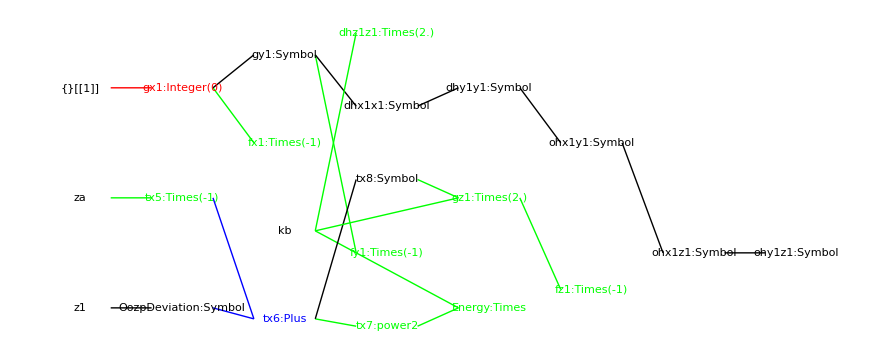

```mathematica
packGraph[oozpPack]
```

## Harmonic potential between a point and a line (specified by two points Xa, Xb) - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,ka];
```

```mathematica
bx = { x1, y1, z1};
ba = { xa, ya, za };
bb = { xb, yb, zb };
```

```mathematica
dtop = Sqrt[Cross[(bx-ba),(bx-bb)].Cross[(bx-ba),(bx-bb)]];
```

```mathematica
√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)
```

√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)

```mathematica
dbottom = Sqrt[(bb-ba).(bb-ba)];
```

```mathematica
√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)
```

√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)

```mathematica
pointToLineEnergyFn =  ka  (dtop/dbottom-ra)^2
```

ka (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)))^2

```mathematica
names = Flatten[{bx}]
```

{x1,y1,z1}

### Energy function

```mathematica
pointToLineVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
pointToLineSetupRules = {};
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);"]];AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);"]];
AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);"]];AppendTo[pointToLineSetupRules,CCode["POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);"]];
```

```mathematica
For[i=1,i≤Length[pointToLineVarNames],i++,
str = "POINT_TO_LINE_RESTRAINT_SET_POSITION("<>ToString[pointToLineVarNames[[i]][[1]]]<>","<>ToString[pointToLineVarNames[[i]][[3]]]<>","<>ToString[pointToLineVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[pointToLineSetupRules,CCode[str]];
];
```

POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);

POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);

POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);

```mathematica
pointToLineSetupRules//MatrixForm
```

(CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);])

```mathematica
pointToLineEnergyRules = {};
pointToLineOutputs = {};
AppendTo[pointToLineEnergyRules,Assign[Energy,pointToLineEnergyFn]];
AppendTo[pointToLineEnergyRules,EnergyAccumulate["POINT_TO_LINE_RESTRAINT",Energy]];
AppendTo[pointToLineOutputs,Energy];
```

### Gradient and Hessian

```mathematica
pointToLineEnergyFn
```

ka (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)))^2

```mathematica
(pointToLineHessian = Table[Table[0,{6}],{6}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
pointToLineForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["POINT_TO_LINE_RESTRAINT",pointToLineForceHessianRules,pointToLineOutputs,pointToLineHessian,pointToLineEnergyFn,pointToLineVarNames];
```

```mathematica
pointToLineHessian//MatrixForm
```

(5 | 8 | 9 | 0 | 0 | 0
8 | 6 | 10 | 0 | 0 | 0
9 | 10 | 7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
pointToLineOutputs
```

{Energy,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1}

### Collect terms and convert to C code

```mathematica
pointToLineAllRules ={
pointToLineSetupRules,
pointToLineEnergyRules,
pointToLineForceHessianRules};
```

```mathematica
pointToLineRules = Flatten[pointToLineAllRules];
```

```mathematica
pointToLineRules//MatrixForm
```

(CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]
CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]
pointToLineDeviation→PointToLineDeviation
ka (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)))^2→Energy
CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]
CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]
CCode[if ( calcForce ) {]
(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→gx1
-gx1→fx1
CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]
(ka (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→gy1
-gy1→fy1
CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]
(ka (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→gz1
-gz1→fz1
CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]
CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]
CCode[if ( calcDiagonalHessian ) {]
(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb))^2)/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb))^2 (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(ka (2 (ya-yb)^2+2 (-za+zb)^2) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→dhx1x1
CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]
(ka (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb))^2)/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb))^2 (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(ka (2 (-xa+xb)^2+2 (za-zb)^2) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→dhy1y1
CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]
(ka (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb))^2)/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb))^2 (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(ka (2 (xa-xb)^2+2 (-ya+yb)^2) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→dhz1z1
CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]
CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]
CCode[if ( calcOffDiagonalHessian ) {]
(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)) (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)))/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)) (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(2 ka (-xa+xb) (ya-yb) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→ohx1y1
CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]
(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)) (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)))/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (ya-yb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (-za+zb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)) (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(2 ka (xa-xb) (-za+zb) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→ohx1z1
CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]
(ka (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)))/(2 ((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))-(ka (2 (xa-xb) (xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)+2 (-ya+yb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (2 (-xa+xb) (-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)+2 (za-zb) (-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(2 √((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2)^(3/2))+(2 ka (-ya+yb) (za-zb) (-ra+(√((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2))))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa y1+xb y1+x1 ya-xb ya-x1 yb+xa yb)^2+(xa z1-xb z1-x1 za+xb za+x1 zb-xa zb)^2+(-ya z1+yb z1+y1 za-yb za-y1 zb+ya zb)^2))→ohy1z1
CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]
CCode[} /*if calcOffDiagonalHessian */ ]
CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]
CCode[} /*calcDiagonalHessian */]
CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]
CCode[} /*calcForce */]
CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/])

```mathematica
pointToLineInput = {x1,y1,z1,xa,ya,za,xb,yb,zb,ka,ra};
```

```mathematica
AppendTo[pointToLineOutputs,PointToLineDeviation];
```

```mathematica
pointToLinePack0 = {
Name->"PointToLineRestraint",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1},
HessianStructure->pointToLineHessian,
Rules->pointToLineRules,
Input->pointToLineInput,
Output->pointToLineOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[pointToLinePack0];
```

Writing finite difference debug code to: _PointToLineRestraint_debugFiniteDifference.cc

Writing debug variable declares to: _PointToLineRestraint_debugEvalDeclares.cc

Writing xml output debug code to: _PointToLineRestraint_debugEvalSerialize.cc

Writing set variables debug code to: _PointToLineRestraint_debugEvalSet.cc

pointToLinePack = Block[{PrintTemporary = Print}, packOptimize[pointToLinePack0]];

```mathematica
pointToLinePack = packOptimize[pointToLinePack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

After removal: 

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]



pointToLineDeviation -> PointToLineDeviation



-xa -> tx1



-(xa y1) -> tx2



xb y1 -> tx3



-ya -> tx4



x1 ya -> tx5



-(xb ya) -> tx6



-(x1 yb) -> tx7



xa yb -> tx8



xa z1 -> tx9



-(xb z1) -> tx10



-(ya z1) -> tx11



yb z1 -> tx12



-za -> tx13



-(x1 za) -> tx14



xb za -> tx15



y1 za -> tx16



-(yb za) -> tx17



x1 zb -> tx18



-(xa zb) -> tx19



-(y1 zb) -> tx20



ya zb -> tx21



tx13 x1 -> tx22



tx4 xb -> tx23



tx1 y1 -> tx24



tx13 yb -> tx25



tx4 z1 -> tx26



tx1 zb -> tx27



tx12 + tx16 + tx20 + tx21 + tx25 + tx26 -> tx28



tx23 + tx24 + tx3 + tx5 + tx7 + tx8 -> tx29



tx10 + tx15 + tx18 + tx22 + tx27 + tx9 -> tx30



tx1 + xb -> tx31



tx4 + yb -> tx32



tx13 + zb -> tx33


    2
tx28  -> tx34


    2
tx29  -> tx35


    2
tx30  -> tx36


    2
tx31  -> tx37


    2
tx32  -> tx38


    2
tx33  -> tx39



tx34 + tx35 + tx36 -> tx40



tx37 + tx38 + tx39 -> tx41



Sqrt[tx40] -> tx42

    1
---------- -> tx43
Sqrt[tx41]



-ra -> tx44



tx42 tx43 -> tx45



tx44 + tx45 -> tx46


    2
tx46  -> tx47



ka tx47 -> Energy



CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-yb -> tx48



tx48 + ya -> tx49



2 tx30 tx33 -> tx50



2 tx29 tx49 -> tx51

    1
---------- -> tx52
Sqrt[tx40]



tx50 + tx51 -> tx53



ka tx43 tx46 tx52 tx53 -> gx1



-gx1 -> fx1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]



-zb -> tx54



tx54 + za -> tx55



2 tx29 tx31 -> tx56



2 tx28 tx55 -> tx57



tx56 + tx57 -> tx58



ka tx43 tx46 tx52 tx58 -> gy1



-gy1 -> fy1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]



-xb -> tx59



tx59 + xa -> tx60



2 tx28 tx32 -> tx61



2 tx30 tx60 -> tx62



tx61 + tx62 -> tx63



ka tx43 tx46 tx52 tx63 -> gz1



-gz1 -> fz1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]



CCode[if ( calcDiagonalHessian ) {]


    2
tx49  -> tx64



2 tx39 -> tx65



2 tx64 -> tx66


    -(3/2)
tx40       -> tx67

 1
---- -> tx68
tx40

 1
---- -> tx69
tx41


    2
tx53  -> tx70



tx65 + tx66 -> tx71

-(ka tx43 tx46 tx67 tx70)
------------------------- -> tx72
            2

ka tx68 tx69 tx70
----------------- -> tx73
        2



ka tx43 tx46 tx52 tx71 -> tx74



tx72 + tx73 + tx74 -> dhx1x1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]


    2
tx55  -> tx75



2 tx37 -> tx76



2 tx75 -> tx77


    2
tx58  -> tx78



tx76 + tx77 -> tx79

-(ka tx43 tx46 tx67 tx78)
------------------------- -> tx80
            2

ka tx68 tx69 tx78
----------------- -> tx81
        2



ka tx43 tx46 tx52 tx79 -> tx82



tx80 + tx81 + tx82 -> dhy1y1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]


    2
tx60  -> tx83



2 tx38 -> tx84



2 tx83 -> tx85


    2
tx63  -> tx86



tx84 + tx85 -> tx87

-(ka tx43 tx46 tx67 tx86)
------------------------- -> tx88
            2

ka tx68 tx69 tx86
----------------- -> tx89
        2



ka tx43 tx46 tx52 tx87 -> tx90



tx88 + tx89 + tx90 -> dhz1z1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]



CCode[if ( calcOffDiagonalHessian ) {]



2 ka tx31 tx43 tx46 tx49 tx52 -> tx91

-(ka tx43 tx46 tx53 tx58 tx67)
------------------------------ -> tx92
              2

ka tx53 tx58 tx68 tx69
---------------------- -> tx93
          2



tx91 + tx92 + tx93 -> ohx1y1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]



2 ka tx33 tx43 tx46 tx52 tx60 -> tx94

-(ka tx43 tx46 tx53 tx63 tx67)
------------------------------ -> tx95
              2

ka tx53 tx63 tx68 tx69
---------------------- -> tx96
          2



tx94 + tx95 + tx96 -> ohx1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]



2 ka tx32 tx43 tx46 tx52 tx55 -> tx97

-(ka tx43 tx46 tx58 tx63 tx67)
------------------------------ -> tx98
              2

ka tx58 tx63 tx68 tx69
---------------------- -> tx99
          2



tx97 + tx98 + tx99 -> ohy1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]



CCode[} /*if calcOffDiagonalHessian */ ]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcDiagonalHessian */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcForce */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

Collecting terms

Set::write: Tag Times in Null {Name→PointToLineRestraint,AdditionalCDeclares→,DerivativeVariables→{x1,y1,z1},HessianStructure→{{5,8,9,0,0,0},{8,6,10,0,0,0},{9,10,«2»,0,0},«1»,{0,0,0,0,0,0},{0,0,0,0,0,0}},Rules→{CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);],CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);],CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);],CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);],CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);],«38»,CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/],CCode[} /*calcDiagonalHessian */],CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/],CCode[} /*calcForce */],CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]},Input→{x1,y1,z1,xa,ya,za,xb,yb,zb,ka,ra},Output→{Energy,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1,PointToLineDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

After removal: 

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]



pointToLineDeviation -> PointToLineDeviation



-xa -> tx100



-(xa y1) -> tx101



xb y1 -> tx102



-ya -> tx103



x1 ya -> tx104



-(xb ya) -> tx105



-(x1 yb) -> tx106



xa yb -> tx107



xa z1 -> tx108



-(xb z1) -> tx109



-(ya z1) -> tx110



yb z1 -> tx111



-za -> tx112



-(x1 za) -> tx113



xb za -> tx114



y1 za -> tx115



-(yb za) -> tx116



x1 zb -> tx117



-(xa zb) -> tx118



-(y1 zb) -> tx119



ya zb -> tx120



tx112 x1 -> tx121



tx103 xb -> tx122



tx100 y1 -> tx123



tx112 yb -> tx124



tx103 z1 -> tx125



tx100 zb -> tx126



tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127



tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128



tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129



tx100 + xb -> tx130



tx103 + yb -> tx131



tx112 + zb -> tx132


     2
tx127  -> tx133


     2
tx128  -> tx134


     2
tx129  -> tx135


     2
tx130  -> tx136


     2
tx131  -> tx137


     2
tx132  -> tx138



tx133 + tx134 + tx135 -> tx139



tx136 + tx137 + tx138 -> tx140



Sqrt[tx139] -> tx141

     1
----------- -> tx142
Sqrt[tx140]



-ra -> tx143



tx141 tx142 -> tx144



tx143 + tx144 -> tx145


     2
tx145  -> tx146



ka tx146 -> Energy



CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-yb -> tx147



tx147 + ya -> tx148



2 tx129 tx132 -> tx149



2 tx127 tx148 -> tx150

     1
----------- -> tx151
Sqrt[tx139]



tx149 + tx150 -> tx152



ka tx142 tx145 tx151 tx152 -> gx1



-gx1 -> fx1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]



-zb -> tx153



tx153 + za -> tx154



2 tx127 tx130 -> tx155



2 tx128 tx154 -> tx156



tx155 + tx156 -> tx157



ka tx142 tx145 tx151 tx157 -> gy1



-gy1 -> fy1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]



-xb -> tx158



tx158 + xa -> tx159



2 tx128 tx131 -> tx160



2 tx129 tx159 -> tx161



tx160 + tx161 -> tx162



ka tx142 tx145 tx151 tx162 -> gz1



-gz1 -> fz1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]



CCode[if ( calcDiagonalHessian ) {]


     2
tx148  -> tx163



2 tx138 -> tx164



2 tx163 -> tx165


     -(3/2)
tx139       -> tx166

  1
----- -> tx167
tx139

  1
----- -> tx168
tx140


     2
tx152  -> tx169



tx164 + tx165 -> tx170

-(ka tx142 tx145 tx166 tx169)
----------------------------- -> tx171
              2

ka tx167 tx168 tx169
-------------------- -> tx172
         2



ka tx142 tx145 tx151 tx170 -> tx173



tx171 + tx172 + tx173 -> dhx1x1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]


     2
tx154  -> tx174



2 tx136 -> tx175



2 tx174 -> tx176


     2
tx157  -> tx177



tx175 + tx176 -> tx178

-(ka tx142 tx145 tx166 tx177)
----------------------------- -> tx179
              2

ka tx167 tx168 tx177
-------------------- -> tx180
         2



ka tx142 tx145 tx151 tx178 -> tx181



tx179 + tx180 + tx181 -> dhy1y1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]


     2
tx159  -> tx182



2 tx137 -> tx183



2 tx182 -> tx184


     2
tx162  -> tx185



tx183 + tx184 -> tx186

-(ka tx142 tx145 tx166 tx185)
----------------------------- -> tx187
              2

ka tx167 tx168 tx185
-------------------- -> tx188
         2



ka tx142 tx145 tx151 tx186 -> tx189



tx187 + tx188 + tx189 -> dhz1z1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]



CCode[if ( calcOffDiagonalHessian ) {]



2 ka tx130 tx142 tx145 tx148 tx151 -> tx190

-(ka tx142 tx145 tx152 tx157 tx166)
----------------------------------- -> tx191
                 2

ka tx152 tx157 tx167 tx168
-------------------------- -> tx192
            2



tx190 + tx191 + tx192 -> ohx1y1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]



2 ka tx132 tx142 tx145 tx151 tx159 -> tx193

-(ka tx142 tx145 tx152 tx162 tx166)
----------------------------------- -> tx194
                 2

ka tx152 tx162 tx167 tx168
-------------------------- -> tx195
            2



tx193 + tx194 + tx195 -> ohx1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]



2 ka tx131 tx142 tx145 tx151 tx154 -> tx196

-(ka tx142 tx145 tx157 tx162 tx166)
----------------------------------- -> tx197
                 2

ka tx157 tx162 tx167 tx168
-------------------------- -> tx198
            2



tx196 + tx197 + tx198 -> ohy1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]



CCode[} /*if calcOffDiagonalHessian */ ]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcDiagonalHessian */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcForce */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation, tx113 -> tx121, tx105 -> tx122, tx101 -> tx123, tx116 -> tx124, tx110 -> tx125, tx118 -> tx126}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

After removal: 

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]



CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]



CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]



pointToLineDeviation -> PointToLineDeviation



-xa -> tx100



tx100 y1 -> tx101



xb y1 -> tx102



-ya -> tx103



x1 ya -> tx104



tx103 xb -> tx105



-(x1 yb) -> tx106



xa yb -> tx107



xa z1 -> tx108



-(xb z1) -> tx109



tx103 z1 -> tx110



yb z1 -> tx111



-za -> tx112



tx112 x1 -> tx113



xb za -> tx114



y1 za -> tx115



tx112 yb -> tx116



x1 zb -> tx117



tx100 zb -> tx118



-(y1 zb) -> tx119



ya zb -> tx120



tx113 -> tx121



tx105 -> tx122



tx101 -> tx123



tx116 -> tx124



tx110 -> tx125



tx118 -> tx126



tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127



tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128



tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129



tx100 + xb -> tx130



tx103 + yb -> tx131



tx112 + zb -> tx132



power2[tx127] -> tx133



power2[tx128] -> tx134



power2[tx129] -> tx135



power2[tx130] -> tx136



power2[tx131] -> tx137



power2[tx132] -> tx138



tx133 + tx134 + tx135 -> tx139



tx136 + tx137 + tx138 -> tx140



mysqrt[tx139] -> tx141



mysqrt[tx140] -> tx199



reciprocal[tx199] -> tx142



-ra -> tx143



tx141 tx142 -> tx144



tx143 + tx144 -> tx145



power2[tx145] -> tx146



ka tx146 -> Energy



CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]



CCode[if ( calcForce ) {]



-yb -> tx147



tx147 + ya -> tx148



2. tx129 tx132 -> tx149



2. tx127 tx148 -> tx150



reciprocal[tx141] -> tx151



tx149 + tx150 -> tx152



ka tx142 tx145 tx151 tx152 -> gx1



-gx1 -> fx1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]



-zb -> tx153



tx153 + za -> tx154



2. tx127 tx130 -> tx155



2. tx128 tx154 -> tx156



tx155 + tx156 -> tx157



ka tx142 tx145 tx151 tx157 -> gy1



-gy1 -> fy1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]



-xb -> tx158



tx158 + xa -> tx159



2. tx128 tx131 -> tx160



2. tx129 tx159 -> tx161



tx160 + tx161 -> tx162



ka tx142 tx145 tx151 tx162 -> gz1



-gz1 -> fz1



CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]



CCode[if ( calcDiagonalHessian ) {]



power2[tx148] -> tx163



2. tx138 -> tx164



2. tx163 -> tx165



power1[tx139] -> tx200

  1
----- -> tx201
tx141

  1
----- -> tx202
tx200



1. tx201 tx202 -> tx166



reciprocal[tx139] -> tx167



reciprocal[tx140] -> tx168



power2[tx152] -> tx169



tx164 + tx165 -> tx170



-0.5 ka tx142 tx145 tx166 tx169 -> tx171



0.5 ka tx167 tx168 tx169 -> tx172



ka tx142 tx145 tx151 tx170 -> tx173



tx171 + tx172 + tx173 -> dhx1x1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]



power2[tx154] -> tx174



2. tx136 -> tx175



2. tx174 -> tx176



power2[tx157] -> tx177



tx175 + tx176 -> tx178



-0.5 ka tx142 tx145 tx166 tx177 -> tx179



0.5 ka tx167 tx168 tx177 -> tx180



ka tx142 tx145 tx151 tx178 -> tx181



tx179 + tx180 + tx181 -> dhy1y1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]



power2[tx159] -> tx182



2. tx137 -> tx183



2. tx182 -> tx184



power2[tx162] -> tx185



tx183 + tx184 -> tx186



-0.5 ka tx142 tx145 tx166 tx185 -> tx187



0.5 ka tx167 tx168 tx185 -> tx188



ka tx142 tx145 tx151 tx186 -> tx189



tx187 + tx188 + tx189 -> dhz1z1



CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]



CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]



CCode[if ( calcOffDiagonalHessian ) {]



2. ka tx130 tx142 tx145 tx148 tx151 -> tx190



-0.5 ka tx142 tx145 tx152 tx157 tx166 -> tx191



0.5 ka tx152 tx157 tx167 tx168 -> tx192



tx190 + tx191 + tx192 -> ohx1y1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]



2. ka tx132 tx142 tx145 tx151 tx159 -> tx193



-0.5 ka tx142 tx145 tx152 tx162 tx166 -> tx194



0.5 ka tx152 tx162 tx167 tx168 -> tx195



tx193 + tx194 + tx195 -> ohx1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]



2. ka tx131 tx142 tx145 tx151 tx154 -> tx196



-0.5 ka tx142 tx145 tx157 tx162 tx166 -> tx197



0.5 ka tx157 tx162 tx167 tx168 -> tx198



tx196 + tx197 + tx198 -> ohy1z1



CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]



CCode[} /*if calcOffDiagonalHessian */ ]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcDiagonalHessian */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]



CCode[} /*calcForce */]



CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation, tx113 -> tx121, tx105 -> tx122, tx101 -> tx123, tx116 -> tx124, tx110 -> tx125, tx118 -> tx126, tx139 -> tx200, tx151 -> tx201, tx202 -> tx167}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx139 -> tx200

tx151 -> tx201

tx202 -> tx167

After removal: CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]

pointToLineDeviation -> PointToLineDeviation

-xa -> tx100

tx100 y1 -> tx101

xb y1 -> tx102

-ya -> tx103

x1 ya -> tx104

tx103 xb -> tx105

-(x1 yb) -> tx106

xa yb -> tx107

xa z1 -> tx108

-(xb z1) -> tx109

tx103 z1 -> tx110

yb z1 -> tx111

-za -> tx112

tx112 x1 -> tx113

xb za -> tx114

y1 za -> tx115

tx112 yb -> tx116

x1 zb -> tx117

tx100 zb -> tx118

-(y1 zb) -> tx119

ya zb -> tx120

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127

tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128

tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129

tx100 + xb -> tx130

tx103 + yb -> tx131

tx112 + zb -> tx132

power2[tx127] -> tx133

power2[tx128] -> tx134

power2[tx129] -> tx135

power2[tx130] -> tx136

power2[tx131] -> tx137

power2[tx132] -> tx138

tx133 + tx134 + tx135 -> tx139

tx136 + tx137 + tx138 -> tx140

mysqrt[tx139] -> tx141

mysqrt[tx140] -> tx199

reciprocal[tx199] -> tx142

-ra -> tx143

tx141 tx142 -> tx144

tx143 + tx144 -> tx145

power2[tx145] -> tx146

ka tx146 -> Energy

CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]

CCode[if ( calcForce ) {]

-yb -> tx147

tx147 + ya -> tx148

2. tx129 tx132 -> tx149

2. tx127 tx148 -> tx150

reciprocal[tx141] -> tx151

tx149 + tx150 -> tx152

ka tx142 tx145 tx151 tx152 -> gx1

-gx1 -> fx1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]

-zb -> tx153

tx153 + za -> tx154

2. tx127 tx130 -> tx155

2. tx128 tx154 -> tx156

tx155 + tx156 -> tx157

ka tx142 tx145 tx151 tx157 -> gy1

-gy1 -> fy1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]

-xb -> tx158

tx158 + xa -> tx159

2. tx128 tx131 -> tx160

2. tx129 tx159 -> tx161

tx160 + tx161 -> tx162

ka tx142 tx145 tx151 tx162 -> gz1

-gz1 -> fz1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx148] -> tx163

2. tx138 -> tx164

2. tx163 -> tx165

tx139 -> tx200

tx151 -> tx201

reciprocal[tx200] -> tx202

tx201 tx202 -> tx166

tx202 -> tx167

reciprocal[tx140] -> tx168

power2[tx152] -> tx169

tx164 + tx165 -> tx170

-0.5 ka tx142 tx145 tx166 tx169 -> tx171

0.5 ka tx167 tx168 tx169 -> tx172

ka tx142 tx145 tx170 tx201 -> tx173

tx171 + tx172 + tx173 -> dhx1x1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

power2[tx154] -> tx174

2. tx136 -> tx175

2. tx174 -> tx176

power2[tx157] -> tx177

tx175 + tx176 -> tx178

-0.5 ka tx142 tx145 tx166 tx177 -> tx179

0.5 ka tx167 tx168 tx177 -> tx180

ka tx142 tx145 tx178 tx201 -> tx181

tx179 + tx180 + tx181 -> dhy1y1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

power2[tx159] -> tx182

2. tx137 -> tx183

2. tx182 -> tx184

power2[tx162] -> tx185

tx183 + tx184 -> tx186

-0.5 ka tx142 tx145 tx166 tx185 -> tx187

0.5 ka tx167 tx168 tx185 -> tx188

ka tx142 tx145 tx186 tx201 -> tx189

tx187 + tx188 + tx189 -> dhz1z1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

2. ka tx130 tx142 tx145 tx148 tx201 -> tx190

-0.5 ka tx142 tx145 tx152 tx157 tx166 -> tx191

0.5 ka tx152 tx157 tx167 tx168 -> tx192

tx190 + tx191 + tx192 -> ohx1y1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

2. ka tx132 tx142 tx145 tx159 tx201 -> tx193

-0.5 ka tx142 tx145 tx152 tx162 tx166 -> tx194

0.5 ka tx152 tx162 tx167 tx168 -> tx195

tx193 + tx194 + tx195 -> ohx1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

2. ka tx131 tx142 tx145 tx154 tx201 -> tx196

-0.5 ka tx142 tx145 tx157 tx162 tx166 -> tx197

0.5 ka tx157 tx162 tx167 tx168 -> tx198

tx196 + tx197 + tx198 -> ohy1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation, tx113 -> tx121, tx105 -> tx122, tx101 -> tx123, tx116 -> tx124, tx110 -> tx125, tx118 -> tx126, tx139 -> tx200, tx151 -> tx201, tx202 -> tx167}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx139 -> tx200

tx151 -> tx201

tx202 -> tx167

After removal: CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]

pointToLineDeviation -> PointToLineDeviation

-xa -> tx100

tx100 y1 -> tx101

xb y1 -> tx102

-ya -> tx103

x1 ya -> tx104

tx103 xb -> tx105

-(x1 yb) -> tx106

xa yb -> tx107

xa z1 -> tx108

-(xb z1) -> tx109

tx103 z1 -> tx110

yb z1 -> tx111

-za -> tx112

tx112 x1 -> tx113

xb za -> tx114

y1 za -> tx115

tx112 yb -> tx116

x1 zb -> tx117

tx100 zb -> tx118

-(y1 zb) -> tx119

ya zb -> tx120

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127

tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128

tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129

tx100 + xb -> tx130

tx103 + yb -> tx131

tx112 + zb -> tx132

power2[tx127] -> tx133

power2[tx128] -> tx134

power2[tx129] -> tx135

power2[tx130] -> tx136

power2[tx131] -> tx137

power2[tx132] -> tx138

tx133 + tx134 + tx135 -> tx139

tx136 + tx137 + tx138 -> tx140

mysqrt[tx139] -> tx141

mysqrt[tx140] -> tx199

reciprocal[tx199] -> tx142

-ra -> tx143

tx141 tx142 -> tx144

tx143 + tx144 -> tx145

power2[tx145] -> tx146

ka tx146 -> Energy

CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]

CCode[if ( calcForce ) {]

-yb -> tx147

tx147 + ya -> tx148

2. tx129 -> tzz216

tx132 tzz216 -> tx149

2. tx127 -> tzz218

tx148 tzz218 -> tx150

reciprocal[tx141] -> tx151

tx149 + tx150 -> tx152

tx142 tx145 -> tzz203

ka tzz203 -> tzz204

tx151 tzz204 -> tzz211

tx152 tzz211 -> gx1

-gx1 -> fx1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]

-zb -> tx153

tx153 + za -> tx154

tx130 tzz218 -> tx155

2. tx128 -> tzz217

tx154 tzz217 -> tx156

tx155 + tx156 -> tx157

tx157 tzz211 -> gy1

-gy1 -> fy1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]

-xb -> tx158

tx158 + xa -> tx159

tx131 tzz217 -> tx160

tx159 tzz216 -> tx161

tx160 + tx161 -> tx162

tx162 tzz211 -> gz1

-gz1 -> fz1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx148] -> tx163

2. tx138 -> tx164

2. tx163 -> tx165

tx139 -> tx200

tx151 -> tx201

reciprocal[tx200] -> tx202

tx201 tx202 -> tx166

tx202 -> tx167

reciprocal[tx140] -> tx168

power2[tx152] -> tx169

tx164 + tx165 -> tx170

tx166 tzz204 -> tzz207

-0.5 tzz207 -> tzz210

tx169 tzz210 -> tx171

tx167 tx168 -> tzz206

ka tzz206 -> tzz208

0.5 tzz208 -> tzz209

tx169 tzz209 -> tx172

tx201 tzz204 -> tzz205

tx170 tzz205 -> tx173

tx171 + tx172 + tx173 -> dhx1x1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

power2[tx154] -> tx174

2. tx136 -> tx175

2. tx174 -> tx176

power2[tx157] -> tx177

tx175 + tx176 -> tx178

tx177 tzz210 -> tx179

tx177 tzz209 -> tx180

tx178 tzz205 -> tx181

tx179 + tx180 + tx181 -> dhy1y1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

power2[tx159] -> tx182

2. tx137 -> tx183

2. tx182 -> tx184

power2[tx162] -> tx185

tx183 + tx184 -> tx186

tx185 tzz210 -> tx187

tx185 tzz209 -> tx188

tx186 tzz205 -> tx189

tx187 + tx188 + tx189 -> dhz1z1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

2. tzz205 -> tzz212

tx130 tx148 tzz212 -> tx190

tx152 tx157 -> tzz215

tzz210 tzz215 -> tx191

tzz209 tzz215 -> tx192

tx190 + tx191 + tx192 -> ohx1y1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx132 tx159 tzz212 -> tx193

tx162 tzz210 -> tzz213

tx152 tzz213 -> tx194

tx162 tzz209 -> tzz214

tx152 tzz214 -> tx195

tx193 + tx194 + tx195 -> ohx1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

tx131 tx154 tzz212 -> tx196

tx157 tzz213 -> tx197

tx157 tzz214 -> tx198

tx196 + tx197 + tx198 -> ohy1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation, tx113 -> tx121, tx105 -> tx122, tx101 -> tx123, tx116 -> tx124, tx110 -> tx125, tx118 -> tx126, tx139 -> tx200, tx151 -> tx201, tx202 -> tx167}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx139 -> tx200

tx151 -> tx201

tx202 -> tx167

After removal: CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]

pointToLineDeviation -> PointToLineDeviation

-xa -> tx100

tx100 y1 -> tx101

xb y1 -> tx102

-ya -> tx103

x1 ya -> tx104

tx103 xb -> tx105

-(x1 yb) -> tx106

xa yb -> tx107

xa z1 -> tx108

-(xb z1) -> tx109

tx103 z1 -> tx110

yb z1 -> tx111

-za -> tx112

tx112 x1 -> tx113

xb za -> tx114

y1 za -> tx115

tx112 yb -> tx116

x1 zb -> tx117

tx100 zb -> tx118

-(y1 zb) -> tx119

ya zb -> tx120

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127

tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128

tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129

tx100 + xb -> tx130

tx103 + yb -> tx131

tx112 + zb -> tx132

power2[tx127] -> tx133

power2[tx128] -> tx134

power2[tx129] -> tx135

power2[tx130] -> tx136

power2[tx131] -> tx137

power2[tx132] -> tx138

tx133 + tx134 + tx135 -> tx139

tx136 + tx137 + tx138 -> tx140

mysqrt[tx139] -> tx141

mysqrt[tx140] -> tx199

reciprocal[tx199] -> tx142

-ra -> tx143

tx141 tx142 -> tx144

tx143 + tx144 -> tx145

power2[tx145] -> tx146

ka tx146 -> Energy

CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]

CCode[if ( calcForce ) {]

-yb -> tx147

tx147 + ya -> tx148

2. tx129 -> tzz216

tx132 tzz216 -> tx149

2. tx127 -> tzz218

tx148 tzz218 -> tx150

reciprocal[tx141] -> tx151

tx149 + tx150 -> tx152

tx142 tx145 -> tzz203

ka tzz203 -> tzz204

tx151 tzz204 -> tzz211

tx152 tzz211 -> gx1

-gx1 -> fx1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]

-zb -> tx153

tx153 + za -> tx154

tx130 tzz218 -> tx155

2. tx128 -> tzz217

tx154 tzz217 -> tx156

tx155 + tx156 -> tx157

tx157 tzz211 -> gy1

-gy1 -> fy1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]

-xb -> tx158

tx158 + xa -> tx159

tx131 tzz217 -> tx160

tx159 tzz216 -> tx161

tx160 + tx161 -> tx162

tx162 tzz211 -> gz1

-gz1 -> fz1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx148] -> tx163

2. tx138 -> tx164

2. tx163 -> tx165

tx139 -> tx200

tx151 -> tx201

reciprocal[tx200] -> tx202

tx201 tx202 -> tx166

tx202 -> tx167

reciprocal[tx140] -> tx168

power2[tx152] -> tx169

tx164 + tx165 -> tx170

tx166 tzz204 -> tzz207

-0.5 tzz207 -> tzz210

tx169 tzz210 -> tx171

tx167 tx168 -> tzz206

ka tzz206 -> tzz208

0.5 tzz208 -> tzz209

tx169 tzz209 -> tx172

tx201 tzz204 -> tzz205

tx170 tzz205 -> tx173

tx171 + tx172 + tx173 -> dhx1x1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

power2[tx154] -> tx174

2. tx136 -> tx175

2. tx174 -> tx176

power2[tx157] -> tx177

tx175 + tx176 -> tx178

tx177 tzz210 -> tx179

tx177 tzz209 -> tx180

tx178 tzz205 -> tx181

tx179 + tx180 + tx181 -> dhy1y1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

power2[tx159] -> tx182

2. tx137 -> tx183

2. tx182 -> tx184

power2[tx162] -> tx185

tx183 + tx184 -> tx186

tx185 tzz210 -> tx187

tx185 tzz209 -> tx188

tx186 tzz205 -> tx189

tx187 + tx188 + tx189 -> dhz1z1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

2. tzz205 -> tzz212

tx130 tx148 tzz212 -> tx190

tx152 tx157 -> tzz215

tzz210 tzz215 -> tx191

tzz209 tzz215 -> tx192

tx190 + tx191 + tx192 -> ohx1y1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx132 tx159 tzz212 -> tx193

tx162 tzz210 -> tzz213

tx152 tzz213 -> tx194

tx162 tzz209 -> tzz214

tx152 tzz214 -> tx195

tx193 + tx194 + tx195 -> ohx1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

tx131 tx154 tzz212 -> tx196

tx157 tzz213 -> tx197

tx157 tzz214 -> tx198

tx196 + tx197 + tx198 -> ohy1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

trivialRules>> triv = {pointToLineDeviation -> PointToLineDeviation, tx113 -> tx121, tx105 -> tx122, tx101 -> tx123, tx116 -> tx124, tx110 -> tx125, tx118 -> tx126, tx139 -> tx200, tx151 -> tx201, tx202 -> tx167}

trivialRules>> outs = {Energy, fx1, fy1, fz1, dhx1x1, dhy1y1, dhz1z1, ohx1y1, ohx1z1, ohy1z1, PointToLineDeviation}

Trivial rules are being removed: pointToLineDeviation -> PointToLineDeviation

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx139 -> tx200

tx151 -> tx201

tx202 -> tx167

After removal: CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ka);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ra);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xa);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(ya);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(za);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(xb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(yb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(zb);]

CCode[POINT_TO_LINE_RESTRAINT_SET_PARAMETER(I1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(x1,I1,0);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(y1,I1,1);]

CCode[POINT_TO_LINE_RESTRAINT_SET_POSITION(z1,I1,2);]

pointToLineDeviation -> PointToLineDeviation

-xa -> tx100

tx100 y1 -> tx101

xb y1 -> tx102

-ya -> tx103

x1 ya -> tx104

tx103 xb -> tx105

-(x1 yb) -> tx106

xa yb -> tx107

xa z1 -> tx108

-(xb z1) -> tx109

tx103 z1 -> tx110

yb z1 -> tx111

-za -> tx112

tx112 x1 -> tx113

xb za -> tx114

y1 za -> tx115

tx112 yb -> tx116

x1 zb -> tx117

tx100 zb -> tx118

-(y1 zb) -> tx119

ya zb -> tx120

tx113 -> tx121

tx105 -> tx122

tx101 -> tx123

tx116 -> tx124

tx110 -> tx125

tx118 -> tx126

tx102 + tx104 + tx106 + tx107 + tx122 + tx123 -> tx127

tx111 + tx115 + tx119 + tx120 + tx124 + tx125 -> tx128

tx108 + tx109 + tx114 + tx117 + tx121 + tx126 -> tx129

tx100 + xb -> tx130

tx103 + yb -> tx131

tx112 + zb -> tx132

power2[tx127] -> tx133

power2[tx128] -> tx134

power2[tx129] -> tx135

power2[tx130] -> tx136

power2[tx131] -> tx137

power2[tx132] -> tx138

tx133 + tx134 + tx135 -> tx139

tx136 + tx137 + tx138 -> tx140

mysqrt[tx139] -> tx141

mysqrt[tx140] -> tx199

reciprocal[tx199] -> tx142

-ra -> tx143

tx141 tx142 -> tx144

tx143 + tx144 -> tx145

power2[tx145] -> tx146

ka tx146 -> Energy

CCode[POINT_TO_LINE_RESTRAINT_ENERGY_ACCUMULATE(Energy);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_FORCE //[]

CCode[if ( calcForce ) {]

-yb -> tx147

tx147 + ya -> tx148

2. tx129 -> tzz216

tx132 tzz216 -> tx149

2. tx127 -> tzz218

tx148 tzz218 -> tx150

reciprocal[tx141] -> tx151

tx149 + tx150 -> tx152

tx142 tx145 -> tzz203

ka tzz203 -> tzz204

tx151 tzz204 -> tzz211

tx152 tzz211 -> gx1

-gx1 -> fx1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]

-zb -> tx153

tx153 + za -> tx154

tx130 tzz218 -> tx155

2. tx128 -> tzz217

tx154 tzz217 -> tx156

tx155 + tx156 -> tx157

tx157 tzz211 -> gy1

-gy1 -> fy1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]

-xb -> tx158

tx158 + xa -> tx159

tx131 tzz217 -> tx160

tx159 tzz216 -> tx161

tx160 + tx161 -> tx162

tx162 tzz211 -> gz1

-gz1 -> fz1

CCode[POINT_TO_LINE_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx148] -> tx163

2. tx138 -> tx164

2. tx163 -> tx165

tx139 -> tx200

tx151 -> tx201

reciprocal[tx200] -> tx202

tx201 tx202 -> tx166

tx202 -> tx167

reciprocal[tx140] -> tx168

power2[tx152] -> tx169

tx164 + tx165 -> tx170

tx166 tzz204 -> tzz207

-0.5 tzz207 -> tzz210

tx169 tzz210 -> tx171

tx167 tx168 -> tzz206

ka tzz206 -> tzz208

0.5 tzz208 -> tzz209

tx169 tzz209 -> tx172

tx201 tzz204 -> tzz205

tx170 tzz205 -> tx173

tx171 + tx172 + tx173 -> dhx1x1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

power2[tx154] -> tx174

2. tx136 -> tx175

2. tx174 -> tx176

power2[tx157] -> tx177

tx175 + tx176 -> tx178

tx177 tzz210 -> tx179

tx177 tzz209 -> tx180

tx178 tzz205 -> tx181

tx179 + tx180 + tx181 -> dhy1y1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

power2[tx159] -> tx182

2. tx137 -> tx183

2. tx182 -> tx184

power2[tx162] -> tx185

tx183 + tx184 -> tx186

tx185 tzz210 -> tx187

tx185 tzz209 -> tx188

tx186 tzz205 -> tx189

tx187 + tx188 + tx189 -> dhz1z1

CCode[POINT_TO_LINE_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

CCode[#ifdef POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

2. tzz205 -> tzz212

tx130 tx148 tzz212 -> tx190

tx152 tx157 -> tzz215

tzz210 tzz215 -> tx191

tzz209 tzz215 -> tx192

tx190 + tx191 + tx192 -> ohx1y1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx132 tx159 tzz212 -> tx193

tx162 tzz210 -> tzz213

tx152 tzz213 -> tx194

tx162 tzz209 -> tzz214

tx152 tzz214 -> tx195

tx193 + tx194 + tx195 -> ohx1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

tx131 tx154 tzz212 -> tx196

tx157 tzz213 -> tx197

tx157 tzz214 -> tx198

tx196 + tx197 + tx198 -> ohy1z1

CCode[POINT_TO_LINE_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* POINT_TO_LINE_RESTRAINT_CALC_FORCE ]*/]

Writing declares to file: _PointToLineRestraint_termDeclares.cc

Writing code to file: _PointToLineRestraint_termCode.cc

Ignore errors in packGraph[pointToLinePack], I forget what it doesn't like but it is something non-essential

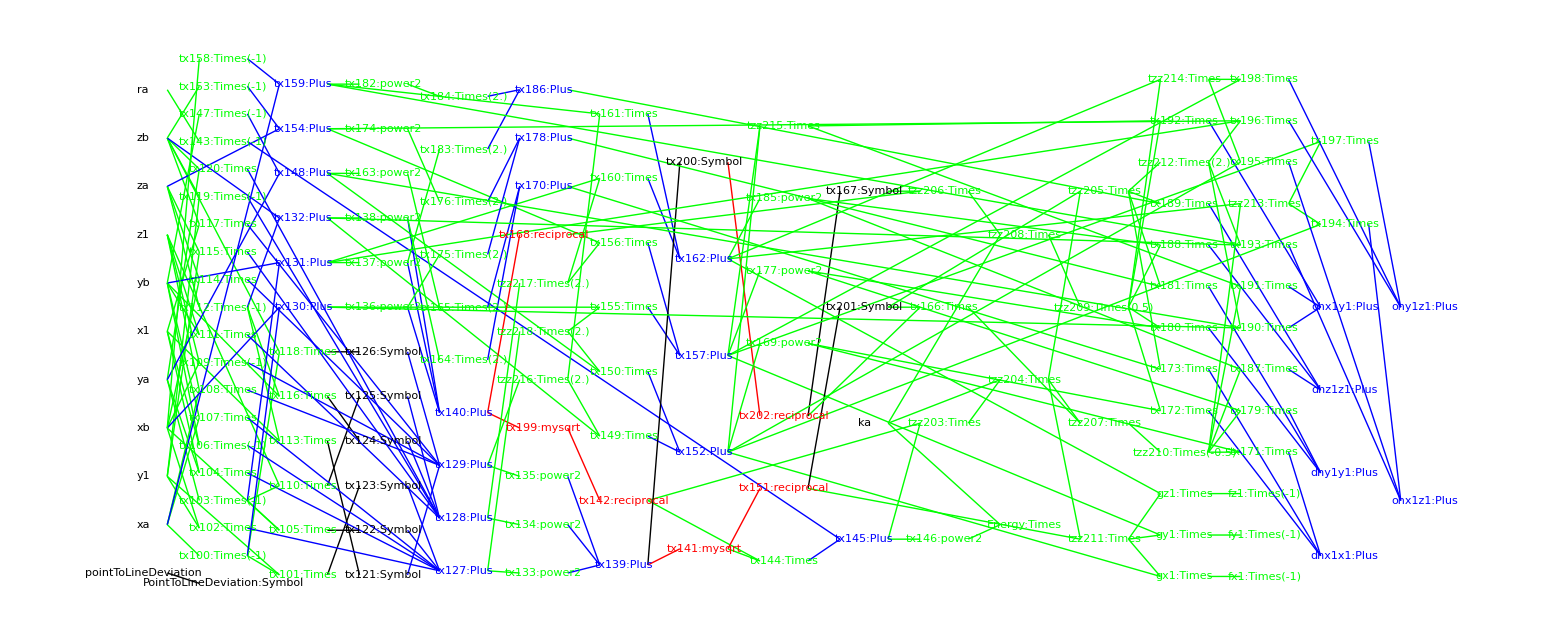

```mathematica
packGraph[pointToLinePack]
```

## Sketch Non-bonding terms Repulsive term for 2d sketches - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,x2,y2,z2, crep];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
erepInputs = Flatten[{ba,bb,crep}]
```

{x1,y1,z1,x2,y2,z2,crep}

```mathematica
erepDistance = Sqrt[Dot[(ba-bb),(ba-bb)]];
```

```mathematica
√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)
```

√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)

```mathematica
erepEquation = crep * Log[erepDistance]
```

crep Log[√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)]

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

```mathematica
D[erepEquation,x1]
```

(crep (x1-x2))/((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)

### Energy

```mathematica
erepVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2}
};
```

```mathematica
erepSetupRules = {};
AppendTo[erepSetupRules,CCode["EREP_SET_PARAMETER(I1);"]];
AppendTo[erepSetupRules,CCode["EREP_SET_PARAMETER(I2);"]];AppendTo[erepSetupRules,CCode["EREP_SET_PARAMETER(crep);"]];
```

```mathematica
For[i=1,i≤Length[erepVarNames],i++,
str = "EREP_SET_POSITION("<>ToString[erepVarNames[[i]][[1]]]<>","<>ToString[erepVarNames[[i]][[3]]]<>","<>ToString[erepVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[erepSetupRules,CCode[str]];
];
```

EREP_SET_POSITION(x1,I1,0);

EREP_SET_POSITION(y1,I1,1);

EREP_SET_POSITION(z1,I1,2);

EREP_SET_POSITION(x2,I2,0);

EREP_SET_POSITION(y2,I2,1);

EREP_SET_POSITION(z2,I2,2);

```mathematica
erepSetupRules//MatrixForm
```

(CCode[EREP_SET_PARAMETER(I1);]
CCode[EREP_SET_PARAMETER(I2);]
CCode[EREP_SET_PARAMETER(crep);]
CCode[EREP_SET_POSITION(x1,I1,0);]
CCode[EREP_SET_POSITION(y1,I1,1);]
CCode[EREP_SET_POSITION(z1,I1,2);]
CCode[EREP_SET_POSITION(x2,I2,0);]
CCode[EREP_SET_POSITION(y2,I2,1);]
CCode[EREP_SET_POSITION(z2,I2,2);])

```mathematica
erepEnergyRules = {};
erepOutputs = {};
AppendTo[erepEnergyRules,Assign[ErepDistance,erepDistance]];
AppendTo[erepEnergyRules,CCode["MAYBE_BAIL(ErepDistance);"]];
AppendTo[erepEnergyRules,Assign[Erep,erepEquation]];
AppendTo[erepEnergyRules,EnergyAccumulate["EREP",Erep]];
AppendTo[erepOutputs,Erep];
```

```mathematica
erepHessian = Table[Table[0,{6}],{6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
erepForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["EREP",erepForceHessianRules,erepOutputs,erepHessian,erepEquation,erepVarNames];
```

### Collect and simplify.

```mathematica
AppendTo[erepOutputs,ErepDistance]
```

{Erep,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2,ErepDistance}

```mathematica
erepOutputs//FullForm
```

List[Erep,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2,ErepDistance]

```mathematica
erepRules = Flatten[{erepSetupRules,erepEnergyRules,erepForceHessianRules}];
```

```mathematica
erepPack0 = {
Name->"Erep",
AdditionalCDeclares->"",
EnergyFunction->erepEquation,
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
HessianStructure->erepHessian,
Rules->erepRules,
Input->erepInputs,
Output->erepOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[erepPack0];
```

Writing finite difference debug code to: _Erep_debugFiniteDifference.cc

Writing debug variable declares to: _Erep_debugEvalDeclares.cc

Writing xml output debug code to: _Erep_debugEvalSerialize.cc

Writing set variables debug code to: _Erep_debugEvalSet.cc

```mathematica
erepPack = packOptimize[erepPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null {Name→Erep,«6»,Output→{Erep,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2,ErepDistance}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

There were no trivial rules

trivialRules>> triv = {tzz46 -> tx35}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

Trivial rules are being removed: tzz46 -> tx35

After removal: CCode[EREP_SET_PARAMETER(I1);]

CCode[EREP_SET_PARAMETER(I2);]

CCode[EREP_SET_PARAMETER(crep);]

CCode[EREP_SET_POSITION(x1,I1,0);]

CCode[EREP_SET_POSITION(y1,I1,1);]

CCode[EREP_SET_POSITION(z1,I1,2);]

CCode[EREP_SET_POSITION(x2,I2,0);]

CCode[EREP_SET_POSITION(y2,I2,1);]

CCode[EREP_SET_POSITION(z2,I2,2);]

-x2 -> tx22

-y2 -> tx23

-z2 -> tx24

tx22 + x1 -> tx25

tx23 + y1 -> tx26

tx24 + z1 -> tx27

power2[tx25] -> tx28

power2[tx26] -> tx29

power2[tx27] -> tx30

tx28 + tx29 + tx30 -> tx31

mysqrt[tx31] -> ErepDistance

CCode[MAYBE_BAIL(ErepDistance);]

Log[ErepDistance] -> tx32

crep tx32 -> Erep

CCode[EREP_ENERGY_ACCUMULATE(Erep);]

CCode[#ifdef EREP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

reciprocal[tx31] -> tx33

crep tx33 -> tzz46

tx25 tzz46 -> gx1

-gx1 -> fx1

CCode[EREP_FORCE_ACCUMULATE(I1, 0, fx1 );]

tx26 tzz46 -> gy1

-gy1 -> fy1

CCode[EREP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx27 tzz46 -> gz1

-gz1 -> fz1

CCode[EREP_FORCE_ACCUMULATE(I1, 2, fz1 );]

fx1 -> gx2

-gx2 -> fx2

CCode[EREP_FORCE_ACCUMULATE(I2, 0, fx2 );]

fy1 -> gy2

-gy2 -> fy2

CCode[EREP_FORCE_ACCUMULATE(I2, 1, fy2 );]

fz1 -> gz2

-gz2 -> fz2

CCode[EREP_FORCE_ACCUMULATE(I2, 2, fz2 );]

CCode[#ifdef EREP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx33] -> tx34

tzz46 -> tx35

crep tx34 -> tzz43

-2. tzz43 -> tzz45

tx28 tzz45 -> tx36

tx35 + tx36 -> dhx1x1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

tx29 tzz45 -> tx37

tx35 + tx37 -> dhy1y1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

tx30 tzz45 -> tx38

tx35 + tx38 -> dhz1z1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

dhx1x1 -> dhx2x2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 0, dhx2x2);]

dhy1y1 -> dhy2y2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 1, dhy2y2);]

dhz1z1 -> dhz2z2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 2, I2, 2, dhz2z2);]

CCode[#ifdef EREP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

tx26 tzz45 -> tzz48

tx25 tzz48 -> ohx1y1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx25 tx27 tzz45 -> ohx1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

2. tzz43 -> tzz44

tx28 tzz44 -> tx39

-tx35 -> tx40

tx39 + tx40 -> ohx1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 0, ohx1x2);]

tx25 tx26 tzz44 -> ohx1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 1, ohx1y2);]

tx27 tzz44 -> tzz47

tx25 tzz47 -> ohx1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 2, ohx1z2);]

tx27 tzz48 -> ohy1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

ohx1y2 -> ohy1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 0, ohy1x2);]

tx29 tzz44 -> tx41

tx40 + tx41 -> ohy1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 1, ohy1y2);]

tx26 tzz47 -> ohy1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 2, ohy1z2);]

ohx1z2 -> ohz1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 0, ohz1x2);]

ohy1z2 -> ohz1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 1, ohz1y2);]

tx30 tzz44 -> tx42

tx40 + tx42 -> ohz1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 2, ohz1z2);]

ohx1y1 -> ohx2y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 1, ohx2y2);]

ohx1z1 -> ohx2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 2, ohx2z2);]

ohy1z1 -> ohy2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 2, ohy2z2);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* EREP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* EREP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* EREP_CALC_FORCE ]*/]

eliminateTrivialRules

trivialRules>> triv = {tzz46 -> tx35}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

Trivial rules are being removed: tzz46 -> tx35

After removal: CCode[EREP_SET_PARAMETER(I1);]

CCode[EREP_SET_PARAMETER(I2);]

CCode[EREP_SET_PARAMETER(crep);]

CCode[EREP_SET_POSITION(x1,I1,0);]

CCode[EREP_SET_POSITION(y1,I1,1);]

CCode[EREP_SET_POSITION(z1,I1,2);]

CCode[EREP_SET_POSITION(x2,I2,0);]

CCode[EREP_SET_POSITION(y2,I2,1);]

CCode[EREP_SET_POSITION(z2,I2,2);]

-x2 -> tx22

-y2 -> tx23

-z2 -> tx24

tx22 + x1 -> tx25

tx23 + y1 -> tx26

tx24 + z1 -> tx27

power2[tx25] -> tx28

power2[tx26] -> tx29

power2[tx27] -> tx30

tx28 + tx29 + tx30 -> tx31

mysqrt[tx31] -> ErepDistance

CCode[MAYBE_BAIL(ErepDistance);]

Log[ErepDistance] -> tx32

crep tx32 -> Erep

CCode[EREP_ENERGY_ACCUMULATE(Erep);]

CCode[#ifdef EREP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

reciprocal[tx31] -> tx33

crep tx33 -> tzz46

tx25 tzz46 -> gx1

-gx1 -> fx1

CCode[EREP_FORCE_ACCUMULATE(I1, 0, fx1 );]

tx26 tzz46 -> gy1

-gy1 -> fy1

CCode[EREP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx27 tzz46 -> gz1

-gz1 -> fz1

CCode[EREP_FORCE_ACCUMULATE(I1, 2, fz1 );]

fx1 -> gx2

-gx2 -> fx2

CCode[EREP_FORCE_ACCUMULATE(I2, 0, fx2 );]

fy1 -> gy2

-gy2 -> fy2

CCode[EREP_FORCE_ACCUMULATE(I2, 1, fy2 );]

fz1 -> gz2

-gz2 -> fz2

CCode[EREP_FORCE_ACCUMULATE(I2, 2, fz2 );]

CCode[#ifdef EREP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx33] -> tx34

tzz46 -> tx35

crep tx34 -> tzz43

-2. tzz43 -> tzz45

tx28 tzz45 -> tx36

tx35 + tx36 -> dhx1x1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

tx29 tzz45 -> tx37

tx35 + tx37 -> dhy1y1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

tx30 tzz45 -> tx38

tx35 + tx38 -> dhz1z1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

dhx1x1 -> dhx2x2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 0, dhx2x2);]

dhy1y1 -> dhy2y2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 1, dhy2y2);]

dhz1z1 -> dhz2z2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 2, I2, 2, dhz2z2);]

CCode[#ifdef EREP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

tx26 tzz45 -> tzz48

tx25 tzz48 -> ohx1y1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx25 tx27 tzz45 -> ohx1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

2. tzz43 -> tzz44

tx28 tzz44 -> tx39

-tx35 -> tx40

tx39 + tx40 -> ohx1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 0, ohx1x2);]

tx25 tx26 tzz44 -> ohx1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 1, ohx1y2);]

tx27 tzz44 -> tzz47

tx25 tzz47 -> ohx1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 2, ohx1z2);]

tx27 tzz48 -> ohy1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

ohx1y2 -> ohy1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 0, ohy1x2);]

tx29 tzz44 -> tx41

tx40 + tx41 -> ohy1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 1, ohy1y2);]

tx26 tzz47 -> ohy1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 2, ohy1z2);]

ohx1z2 -> ohz1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 0, ohz1x2);]

ohy1z2 -> ohz1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 1, ohz1y2);]

tx30 tzz44 -> tx42

tx40 + tx42 -> ohz1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 2, ohz1z2);]

ohx1y1 -> ohx2y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 1, ohx2y2);]

ohx1z1 -> ohx2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 2, ohx2z2);]

ohy1z1 -> ohy2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 2, ohy2z2);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* EREP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* EREP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* EREP_CALC_FORCE ]*/]

trivialRules>> triv = {tzz46 -> tx35}

trivialRules>> outs = {Erep, fx1, fy1, fz1, fx2, fy2, fz2, dhx1x1, dhy1y1, dhz1z1, dhx2x2, dhy2y2, dhz2z2, ohx1y1, ohx1z1, ohx1x2, ohx1y2, ohx1z2, ohy1z1, ohy1x2, ohy1y2, ohy1z2, ohz1x2, ohz1y2, ohz1z2, ohx2y2, ohx2z2, ohy2z2, ErepDistance}

Trivial rules are being removed: tzz46 -> tx35

After removal: CCode[EREP_SET_PARAMETER(I1);]

CCode[EREP_SET_PARAMETER(I2);]

CCode[EREP_SET_PARAMETER(crep);]

CCode[EREP_SET_POSITION(x1,I1,0);]

CCode[EREP_SET_POSITION(y1,I1,1);]

CCode[EREP_SET_POSITION(z1,I1,2);]

CCode[EREP_SET_POSITION(x2,I2,0);]

CCode[EREP_SET_POSITION(y2,I2,1);]

CCode[EREP_SET_POSITION(z2,I2,2);]

-x2 -> tx22

-y2 -> tx23

-z2 -> tx24

tx22 + x1 -> tx25

tx23 + y1 -> tx26

tx24 + z1 -> tx27

power2[tx25] -> tx28

power2[tx26] -> tx29

power2[tx27] -> tx30

tx28 + tx29 + tx30 -> tx31

mysqrt[tx31] -> ErepDistance

CCode[MAYBE_BAIL(ErepDistance);]

Log[ErepDistance] -> tx32

crep tx32 -> Erep

CCode[EREP_ENERGY_ACCUMULATE(Erep);]

CCode[#ifdef EREP_CALC_FORCE //[]

CCode[if ( calcForce ) {]

reciprocal[tx31] -> tx33

crep tx33 -> tzz46

tx25 tzz46 -> gx1

-gx1 -> fx1

CCode[EREP_FORCE_ACCUMULATE(I1, 0, fx1 );]

tx26 tzz46 -> gy1

-gy1 -> fy1

CCode[EREP_FORCE_ACCUMULATE(I1, 1, fy1 );]

tx27 tzz46 -> gz1

-gz1 -> fz1

CCode[EREP_FORCE_ACCUMULATE(I1, 2, fz1 );]

fx1 -> gx2

-gx2 -> fx2

CCode[EREP_FORCE_ACCUMULATE(I2, 0, fx2 );]

fy1 -> gy2

-gy2 -> fy2

CCode[EREP_FORCE_ACCUMULATE(I2, 1, fy2 );]

fz1 -> gz2

-gz2 -> fz2

CCode[EREP_FORCE_ACCUMULATE(I2, 2, fz2 );]

CCode[#ifdef EREP_CALC_DIAGONAL_HESSIAN //[]

CCode[if ( calcDiagonalHessian ) {]

power2[tx33] -> tx34

tzz46 -> tx35

crep tx34 -> tzz43

-2. tzz43 -> tzz45

tx28 tzz45 -> tx36

tx35 + tx36 -> dhx1x1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]

tx29 tzz45 -> tx37

tx35 + tx37 -> dhy1y1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]

tx30 tzz45 -> tx38

tx35 + tx38 -> dhz1z1

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]

dhx1x1 -> dhx2x2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 0, dhx2x2);]

dhy1y1 -> dhy2y2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 1, dhy2y2);]

dhz1z1 -> dhz2z2

CCode[EREP_DIAGONAL_HESSIAN_ACCUMULATE(I2, 2, I2, 2, dhz2z2);]

CCode[#ifdef EREP_CALC_OFF_DIAGONAL_HESSIAN //[]

CCode[if ( calcOffDiagonalHessian ) {]

tx26 tzz45 -> tzz48

tx25 tzz48 -> ohx1y1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]

tx25 tx27 tzz45 -> ohx1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]

2. tzz43 -> tzz44

tx28 tzz44 -> tx39

-tx35 -> tx40

tx39 + tx40 -> ohx1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 0, ohx1x2);]

tx25 tx26 tzz44 -> ohx1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 1, ohx1y2);]

tx27 tzz44 -> tzz47

tx25 tzz47 -> ohx1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 2, ohx1z2);]

tx27 tzz48 -> ohy1z1

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]

ohx1y2 -> ohy1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 0, ohy1x2);]

tx29 tzz44 -> tx41

tx40 + tx41 -> ohy1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 1, ohy1y2);]

tx26 tzz47 -> ohy1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 2, ohy1z2);]

ohx1z2 -> ohz1x2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 0, ohz1x2);]

ohy1z2 -> ohz1y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 1, ohz1y2);]

tx30 tzz44 -> tx42

tx40 + tx42 -> ohz1z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 2, ohz1z2);]

ohx1y1 -> ohx2y2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 1, ohx2y2);]

ohx1z1 -> ohx2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 2, ohx2z2);]

ohy1z1 -> ohy2z2

CCode[EREP_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 2, ohy2z2);]

CCode[} /*if calcOffDiagonalHessian */ ]

CCode[#endif /* EREP_CALC_OFF_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcDiagonalHessian */]

CCode[#endif /* EREP_CALC_DIAGONAL_HESSIAN ]*/]

CCode[} /*calcForce */]

CCode[#endif /* EREP_CALC_FORCE ]*/]

Writing declares to file: _Erep_termDeclares.cc

Writing code to file: _Erep_termCode.cc

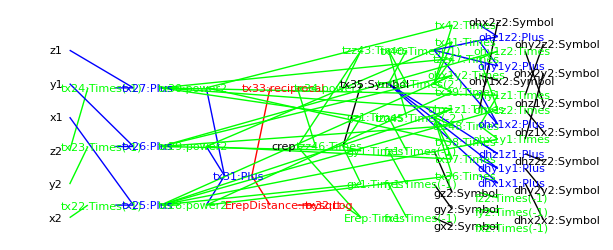

```mathematica
packGraph[erepPack]
```